# precession v2: equation generator

## Davide Gerosa

## This is a notebook to derive the equations describing the dynamics of precessing black-hole binaries at 2PN.

Export expressions in a format that python and numpy are going to like. Use a modified version of the package by Gustavo Wiederhecker  https://github.com/gwiederhecker/ToPython, supplemented by a set of custom transformation for the precession code.  See also  https://mathematica.stackexchange.com/questions/10970/how-to-clear-all-variables-except-one

```mathematica
ToPython[x_,numpyprefix_:"np"]:=Module[{expression=x,greekrule,PythonForm,numpypre=numpyprefix,lp,rp,a,b},
(*By Gustavo Wiederhecker, minor edits by Davide Gerosa.*)
If[numpyprefix=="",sep="",sep="."];
lp="(";
rp=")";
PythonForm[Rational[a_,b_]]:=PythonForm[a]<>"/"<>PythonForm[b];
PythonForm[Complex[a_,b_]]:="complex"<>lp<>PythonForm[a]<>","<>PythonForm[b]<>rp;
PythonForm[Times[a_,b_]]:=PythonForm[a]<>" * "<>PythonForm[b];
PythonForm[Plus[a_,b_]]:=lp<>PythonForm[a]<>" + "<>PythonForm[b]<>rp;
PythonForm[h_[args__]]:=numpypre<>sep<>ToLowerCase[PythonForm[h]]<>lp<>PythonForm[args]<>rp;
PythonForm[Power[a_,b_]]:=lp<>PythonForm[a]<>rp<>"**"<>lp<>PythonForm[b]<>rp;
PythonForm[a_ListQ]:=numpypre<>sep<>"array"<>StringReplace[ToString[a],{"{"-> "[","}"-> "]"}];
PythonForm[Arg]=numpypre<>sep<>"angle";
PythonForm[Csc]:="1/"<>numpypre<>sep<>"sin";
PythonForm[Sec]:="1/"<>numpypre<>sep<>"cos";
PythonForm[Cot]:="1/"<>numpypre<>sep<>"tan";
PythonForm[Csch]:="1/"<>numpypre<>sep<>"sinh";
PythonForm[Sech]:="1/"<>numpypre<>sep<>"cosh";
PythonForm[Coth]:="1/"<>numpypre<>sep<>"tanh";
PythonForm[List[args__]]:=numpypre<>sep<>"array"<>lp<>"["<>Table[PythonForm[{args}[[ii]]]<>",",{ii,1,Length@{args}}]<>"]"<>rp;
PythonForm[π]=numpypre<>sep<>"pi";
PythonForm[E]=numpypre<>sep<>"e";
PythonForm[r_Real]:=Block[{a=MantissaExponent[r]},If[r>=0,ToString[N[a[[1]],6]]<>"e"<>ToString[a[[2]]],"("<>ToString[N[a[[1]],6]]<>"e"<>ToString[a[[2]]]<>")"]];
greekrule={"α"->"alpha","β"->"beta","γ"->"gamma","δ"->"delta","ε"->"curlyepsilon","ζ"->"zeta","η"->"eta","θ"->"theta","ι"->"iota","κ"->"kappa","λ"->"lambda","μ"->"mu","ν"->"nu","ξ"->"xi","ο"->"omicron","π"->"pi","ρ"->"rho","ς"->"finalsigma","σ"->"sigma","τ"->"tau","υ"->"upsilon","φ"->"curlyphi","χ"->"chi","ψ"->"psi","ω"->"omega","Α"->"Alpha","Β"->"Beta","Γ"->"Gamma","Δ"->"Delta","Ε"->"CurlyEpsilon","Ζ"->"Zeta","Η"->"Eta","Θ"->"Theta","Ι"->"Iota","Κ"->"Kappa","Λ"->"Lambda","Μ"->"Mu","Ν"->"Nu","Ξ"->"Xi","Ο"->"Omicron","Π"->"Pi","Ρ"->"Rho","Σ"->"Sigma","Τ"->"Tau","Υ"->"Upsilon","Φ"->"CurlyPhi","Χ"->"Chi","Ψ"->"Psi","Ω"->"Omega"};
PythonForm[allOther_]:=StringReplace[ToString[allOther,FortranForm],greekrule];
PythonForm[expression]];
```

```mathematica
precessionform[label_,expression_]:="# Machine generated with "<>Last@FileNameSplit@NotebookFileName[]<>"\n"<> label<>" = "<>StringReplace[ToPython[expression],{"(q)"->"q","(L)"->"L","(S)"->"S","(J)"->"J","(chi1)"->"chi1","(chi2)"->"chi2","(u)"->"u","(kappa)"->"kappa","(chieff)"->"chieff","(2)"->"2","(3)"->"3","(4)"->"4","(5)"->"5","(6)"->"6","(7)"->"7","(8)"->"8","(9)"->"9","(10)"->"10"}];
```

```mathematica
CurrentValue[$FrontEnd,"NotebookAutoSave"]=True;
```

## (i) S as a function of δχ

```mathematica
Clear@@DeleteCases[Names@"`*","ToPython"|"precessionform"]
```

```mathematica
S1 = χ1 / (1+q)^2
S2 = χ2 q^2 / (1+q)^2
```

χ1/(1+q)^2

(q^2 χ2)/(1+q)^2

```mathematica
cosθ1S = 1/(2(1-q) S1)((J^2-L^2-Ss)/L - 2q χeff/(1+q))
cosθ2S = q/(2(1-q) S2)(-(J^2-L^2-Ss)/L + 2 χeff/(1+q))
```

((1+q)^2 ((J^2-L^2-Ss)/L-(2 q χeff)/(1+q)))/(2 (1-q) χ1)

((1+q)^2 ((-J^2+L^2+Ss)/L+(2 χeff)/(1+q)))/(2 (1-q) q χ2)

```mathematica
deltachi = (χ1 cosθ1x - q χ2 cosθ2x)/(1+q)//Simplify
```

(cosθ1x χ1-cosθ2x q χ2)/(1+q)

```mathematica
Sssol =Ss/. Solve[(deltachi/.cosθ1x->cosθ1S/.cosθ2x->cosθ2S)==δχ, Ss][[1]]//Simplify
```

J^2-(L (L+L q+δχ-q δχ+χeff+q χeff))/(1+q)

Rewritten in a nicer form; check.

```mathematica
Ss= q /(1+q)^2 Sqrt[r]( 2 κ -χeff -δχ (1-q)/(1+q))
```

(q √r (-((1-q) δχ)/(1+q)+2 κ-χeff))/(1+q)^2

```mathematica
L= q /(1+q)^2 Sqrt[r]
κ =(J^2 - L^2) / (2L)
```

(q √r)/(1+q)^2

((1+q)^2 (J^2-(q^2 r)/(1+q)^4))/(2 q √r)

```mathematica
Sssol- Ss//Simplify
```

0

## (i) Spin angles

```mathematica
Clear@@DeleteCases[Names@"`*","ToPython"|"precessionform"]
```

```mathematica
chieff = (χ1 cosθ1x + q χ2 cosθ2x)/(1+q)//Simplify
deltachi = (χ1 cosθ1x - q χ2 cosθ2x)/(1+q)//Simplify
```

(cosθ1x χ1+cosθ2x q χ2)/(1+q)

(cosθ1x χ1-cosθ2x q χ2)/(1+q)

```mathematica
Solve[{chieff==χeff,deltachi==δχ},{cosθ1x,cosθ2x}][[1]]//Simplify
cosθ1sol= cosθ1x/.Out[-1];
cosθ2sol =cosθ2x/.Out[-2];
```

{cosθ1x→((1+q) (δχ+χeff))/(2 χ1),cosθ2x→((1+q) (-δχ+χeff))/(2 q χ2)}

```mathematica
S1 = χ1 / (1+q)^2
S2 = χ2 q^2 / (1+q)^2
L=q /(1+q)^2 Sqrt[r]
```

χ1/(1+q)^2

(q^2 χ2)/(1+q)^2

(q √r)/(1+q)^2

```mathematica
Ss= q /(1+q)^2 Sqrt[r]( 2 κ -χeff -δχ (1-q)/(1+q))
```

(q √r (-((1-q) δχ)/(1+q)+2 κ-χeff))/(1+q)^2

```mathematica
cosθ12sol= (Ss -S1^2-S2^2) / (2S1 S2)//Simplify
```

-(χ1^2+q^4 χ2^2+2 q^2 √r (-2 κ+χeff)+q^3 √r (-δχ-2 κ+χeff)+q √r (δχ-2 κ+χeff))/(2 q^2 χ1 χ2)

```mathematica
cosΔΦsol = (cosθ12sol - cosθ1sol cosθ2sol) / Sqrt[(1-cosθ1sol^2)(1-cosθ2sol^2)]
```

(-((1+q)^2 (-δχ+χeff) (δχ+χeff))/(4 q χ1 χ2)-(χ1^2+q^4 χ2^2+2 q^2 √r (-2 κ+χeff)+q^3 √r (-δχ-2 κ+χeff)+q √r (δχ-2 κ+χeff))/(2 q^2 χ1 χ2))/(√((1-((1+q)^2 (-δχ+χeff)^2)/(4 q^2 χ2^2)) (1-((1+q)^2 (δχ+χeff)^2)/(4 χ1^2))))

Rewritten in a nicer form; check.

```mathematica
cosθ1=((1+q) (χeff+δχ))/(2 χ1)
```

((1+q) (δχ+χeff))/(2 χ1)

```mathematica
cosθ2=((1+q) (χeff-δχ))/(2 q χ2)
```

((1+q) (-δχ+χeff))/(2 q χ2)

```mathematica
cosθ12 =(q (1+q) (2 κ (1+q)- χeff(1+q)-δχ(1-q)) √r - (χ1^2+χ2^2  q^4))/(2 χ1 χ2 q^2)
```

(-χ1^2-q^4 χ2^2+q (1+q) √r (-((1-q) δχ)+2 (1+q) κ-(1+q) χeff))/(2 q^2 χ1 χ2)

```mathematica
cosΔΦ=(2(q (1+q) (2 κ (1+q)-χeff (1+q)-δχ (1-q)) √r) - 2(χ1^2+χ2^2 q^4)-(χeff^2-δχ^2)q (1+q)^2)/(q √((4 χ1^2-(χeff+δχ)^2 (1+q)^2) (4 χ2^2 q^2-(χeff-δχ)^2 (1+q)^2)))
```

(-2 (χ1^2+q^4 χ2^2)+2 q (1+q) √r (-((1-q) δχ)+2 (1+q) κ-(1+q) χeff)-q (1+q)^2 (-δχ^2+χeff^2))/(q √((4 q^2 χ2^2-(1+q)^2 (-δχ+χeff)^2) (4 χ1^2-(1+q)^2 (δχ+χeff)^2)))

```mathematica
cosθ1-cosθ1sol
cosθ2-cosθ2sol
cosθ12-cosθ12sol//Simplify
cosΔΦsol^2-cosΔΦ^2//Simplify
```

0

0

0

«1 more identical outputs»

## (iii) Cubic polynomial (dδχ/dt)^2

```mathematica
Clear@@DeleteCases[Names@"`*","ToPython"|"precessionform"]
```

Prefactor

```mathematica
S1 = χ1 / (1+q)^2;
S2 = χ2 q^2 / (1+q)^2;
L=q /(1+q)^2 Sqrt[r];
J=L Sqrt[L+2κ ];
η=q /(1+q)^2;
```

```mathematica
Ss= q /(1+q)^2 Sqrt[r]( 2 κ -χeff -δχ (1-q)/(1+q))
```

(q √r (-((1-q) δχ)/(1+q)+2 κ-χeff))/(1+q)^2

```mathematica
prefactorsol =- (3((1-q^2)/ q)S1 S2 η^6 / L^5 (1-η χeff/ L)) /  D[Ss,δχ]//Simplify
```

(3 q χ1 χ2 (√r-χeff))/((1+q)^2 r^(7/2))

Rewritten in a nicer form; check.

```mathematica
prefactor =(3 q)/(1+q)^2 χ1 χ2(r)^-3 (1-χeff/(√r))
```

(3 q χ1 χ2 (1-χeff/(√r)))/((1+q)^2 r^3)

```mathematica
prefactorsol-prefactor//Simplify
```

0

Angles

```mathematica
cosΔΦs= (cosθ12 - cosθ1 cosθ2)^2 / ((1-cosθ1 ^2)(1-cosθ2^2))
```

(cosθ12-cosθ1 cosθ2)^2/((1-cosθ1^2) (1-cosθ2^2))

```mathematica
threesines = (1-cosθ1^2)(1-cosθ2^2)(1-cosΔΦs)//Simplify
```

1-cosθ1^2-cosθ12^2+2 cosθ1 cosθ12 cosθ2-cosθ2^2

```mathematica
cosθ1=((1+q) (χeff+δχ))/(2 χ1)
cosθ2=((1+q) (χeff-δχ))/(2 q χ2)
cosθ12 =(q (1+q) (2 κ (1+q)- χeff(1+q)-δχ(1-q)) √r - (χ1^2+χ2^2  q^4))/(2 χ1 χ2 q^2)
```

((1+q) (δχ+χeff))/(2 χ1)

((1+q) (-δχ+χeff))/(2 q χ2)

(-χ1^2-q^4 χ2^2+q (1+q) √r (-((1-q) δχ)+2 (1+q) κ-(1+q) χeff))/(2 q^2 χ1 χ2)

```mathematica
threesines//Simplify
```

-1/(4 q^4 χ1^2 χ2^2)(-4 q^4 χ1^2 χ2^2+(χ1^2+q^4 χ2^2-q (1+q) √r ((-1+q) δχ+(1+q) (2 κ-χeff)))^2+q^2 (1+q)^2 χ1^2 (δχ-χeff)^2-q (1+q)^2 (χ1^2+q^4 χ2^2-q (1+q) √r ((-1+q) δχ+(1+q) (2 κ-χeff))) (δχ-χeff) (δχ+χeff)+q^4 (1+q)^2 χ2^2 (δχ+χeff)^2)

```mathematica
cubic = prefactor^2 threesines//Simplify
```

-1/(4 q^2 (1+q)^4 r^6)9 (-1+χeff/(√r))^2 (-4 q^4 χ1^2 χ2^2+(χ1^2+q^4 χ2^2-q (1+q) √r ((-1+q) δχ+(1+q) (2 κ-χeff)))^2+q^2 (1+q)^2 χ1^2 (δχ-χeff)^2-q (1+q)^2 (χ1^2+q^4 χ2^2-q (1+q) √r ((-1+q) δχ+(1+q) (2 κ-χeff))) (δχ-χeff) (δχ+χeff)+q^4 (1+q)^2 χ2^2 (δχ+χeff)^2)

```mathematica
coeffs = Simplify[CoefficientList[cubic,δχ],q>0&&q<=1&&r>0]
```

{-1/(4 q^2 (1+q)^4 r^7)9 (√r-χeff)^2 (χ1^4+q^8 χ2^4+q χ1^2 (χeff^2+√r (-4 κ+2 χeff))+q^7 χ2^2 (χeff^2+√r (-4 κ+2 χeff))+q^2 (3 χ1^2 χeff^2+r (-2 κ+χeff)^2-√r (2 κ-χeff) (4 χ1^2+χeff^2))+q^4 (χ2^2 χeff^2+6 √r χeff^2 (-2 κ+χeff)+6 r (-2 κ+χeff)^2+χ1^2 (-2 χ2^2+χeff^2))+q^6 (3 χ2^2 χeff^2+r (-2 κ+χeff)^2-√r (2 κ-χeff) (4 χ2^2+χeff^2))+q^3 (3 χ1^2 χeff^2+4 r (-2 κ+χeff)^2-2 √r (2 κ-χeff) (χ1^2+2 χeff^2))+q^5 (3 χ2^2 χeff^2+4 r (-2 κ+χeff)^2-2 √r (2 κ-χeff) (χ2^2+2 χeff^2))),1/(4 q (1+q)^3 r^7)9 (√r-χeff)^2 (-2 √r χ1^2+2 q^5 √r χ2^2+q^2 (4 r κ-2 r χeff+2 χ1^2 χeff-√r χeff^2)+q^3 (-4 r κ+2 r χeff-2 χ2^2 χeff+√r χeff^2)+q (r (4 κ-2 χeff)+2 χ1^2 χeff+√r (2 χ1^2-χeff^2))+q^4 (-2 χ2^2 χeff+r (-4 κ+2 χeff)+√r (-2 χ2^2+χeff^2))),1/(4 q (1+q)^2 r^7)9 (√r-χeff)^2 (χ1^2+q^4 χ2^2-q (r+χ1^2+√r (2 κ-χeff))-q^3 (r+χ2^2+√r (2 κ-χeff))+2 q^2 √r (√r-2 κ+χeff)),-(9 (-1+q) (√r-χeff)^2)/(4 (1+q) r^(13/2))}

```mathematica
Α2sol = coeffs[[4]]/(1-q)//Simplify
```

(9 (√r-χeff)^2)/(4 (1+q) r^(13/2))

```mathematica
Α = 3/2 1/Sqrt[1+q] r^(-11/4 )(1-χeff /Sqrt[r])
```

(3 (1-χeff/(√r)))/(2 √(1+q) r^(11/4))

```mathematica
Α2sol-Α^2//Simplify
```

0

```mathematica
r = ((1+q)^2 / (2 u q ))^2;
```

```mathematica
cubic =Simplify[cubic, q>0&&q<1&&u>0]
```

-1/(1+q)^28 9216 q^10 u^12 (1-(2 q u χeff)/(1+q)^2)^2 (-4 q^4 χ1^2 χ2^2+(χ1^2+q^4 χ2^2-((1+q)^3 ((-1+q) δχ+(1+q) (2 κ-χeff)))/(2 u))^2+q^2 (1+q)^2 χ1^2 (δχ-χeff)^2-q (1+q)^2 (χ1^2+q^4 χ2^2-((1+q)^3 ((-1+q) δχ+(1+q) (2 κ-χeff)))/(2 u)) (δχ-χeff) (δχ+χeff)+q^4 (1+q)^2 χ2^2 (δχ+χeff)^2)

```mathematica
coeffs = Simplify[CoefficientList[cubic,δχ],q>0&&q<=1&&r>0]
```

{1/(1+q)^28 2304 q^10 u^10 (1-(2 q u χeff)/(1+q)^2)^2 (-4 u^2 χ1^4+8 q^4 u^2 χ1^2 χ2^2-4 q^8 u^2 χ2^4+4 (1+q)^4 u χ1^2 (2 κ-χeff)+4 q^4 (1+q)^4 u χ2^2 (2 κ-χeff)-4 q (1+q)^2 u^2 χ1^2 χeff^2-4 q^2 (1+q)^2 u^2 χ1^2 χeff^2-4 q^4 (1+q)^2 u^2 χ2^2 χeff^2-4 q^5 (1+q)^2 u^2 χ2^2 χeff^2+2 q (1+q)^6 u (2 κ-χeff) χeff^2-(1+q)^8 (-2 κ+χeff)^2),1/(1+q)^30 4608 q^10 u^10 (1+q^2+q (2-2 u χeff))^2 (-2 (-1+q) (1+q)^5 κ+(-1+q) (1+q)^5 χeff+4 q^2 u^2 (χ1^2-q^2 χ2^2) χeff+(-1+q^2) u (2 χ1^2+q (2 q^3 χ2^2+χeff^2+2 q χeff^2+q^2 χeff^2))),-1/(1+q)^30 2304 q^10 u^10 (1+q^2+q (2-2 u χeff))^2 (1+q^6+q^2 (-1+16 u κ+4 u^2 χ1^2-8 u χeff)+q^4 (-1+16 u κ+4 u^2 χ2^2-8 u χeff)+4 q^3 (-1+6 u κ-3 u χeff)+q (2+4 u κ-4 u^2 χ1^2-2 u χeff)+q^5 (2+4 u κ-4 u^2 χ2^2-2 u χeff)),-(4608 (-1+q) q^11 u^11 (1+q^2+q (2-2 u χeff))^2)/(1+q)^27}

```mathematica
overall = coeffs[[4]]/((1-q)u)//FullSimplify
```

(4608 q^11 u^10 ((1+q)^2-2 q u χeff)^2)/(1+q)^27

Some simplification by hand to get a nicer form. Define the following  shortcuts:

```mathematica
κtr  = tκ->2 κ-χeff
χtr = {tχ1->χ1^2+q^4 χ2^2,tχ2-> χ1^2 χ2^2,tχ3->(χ1^2 +q^2 χ2^2),tχ4->(χ1^2 -q^2 χ2^2)}
```

tκ→2 κ-χeff

{tχ1→χ1^2+q^4 χ2^2,tχ2→χ1^2 χ2^2,tχ3→χ1^2+q^2 χ2^2,tχ4→χ1^2-q^2 χ2^2}

```mathematica
mycubic= -1/(1+q)^28 9216 q^10 u^12 (1-(2 q u χeff)/(1+q)^2)^2 (-4 q^4 tχ2+(tχ1-((1+q)^3 ((-1+q) δχ+(1+q) tκ))/(2 u))^2-q (1+q)^2 (tχ1-((1+q)^3 ((-1+q) δχ+(1+q) tκ))/(2 u)) (δχ-χeff) (δχ+χeff)+q^2 (1+q)^2 tχ3(δχ^2+χeff^2)-2 q^2 (1+q)^2 tχ4  δχ χeff);
```

```mathematica
mycubic-cubic/.κtr/.χtr//Simplify
```

0

```mathematica
myc = Simplify[CoefficientList[mycubic,δχ]];
```

```mathematica
myc[[4]]/overall //FullSimplify
```

u-q u

```mathematica
myc[[3]]/overall //FullSimplify
```

-((-1+q)^2 (1+q))/(2 q)-(1+q) tκ u+(2 (tχ1-q tχ3) u^2)/(1+q)^3

```mathematica
σ2= -((1-q)^2 (1+q))/(2 q)-u(1+q) (2 κ-χeff) + u^2(2 (1-q) (χ1^2-q^3 χ2^2))/(1+q)^3;
σ2- myc[[3]]/overall /.κtr/.χtr//FullSimplify
σ2== -((1-q)^2 (1+q))/(2 q)-u(1+q) (2 κ-χeff) + u^2(2 (1-q) (χ1^2-q^3 χ2^2))/(1+q)^3//HoldForm//TeXForm
```

0

```mathematica
CoefficientList[myc[[2]]/overall ,u]//Simplify
```

{-((-1+q) (1+q)^2 tκ)/q,((-1+q) (2 tχ1+q (1+q)^2 χeff^2))/(q (1+q)^2),(4 q tχ4 χeff)/(1+q)^3}

```mathematica
σ1= ((1-q) (1+q)^2)/q (2 κ-χeff)-u (1-q)/(q (1+q)^2) (2 (χ1^2+q^4 χ2^2)+q (1+q)^2 χeff^2)+4 u^2 q/(1+q)^3 (χ1^2 -q^2 χ2^2) χeff;
σ1- myc[[2]]/overall /.κtr/.χtr//FullSimplify
σ1== ((1-q) (1+q)^2)/q (2 κ-χeff)-u (1-q)/(q (1+q)^2) (2 (χ1^2+q^4 χ2^2)+q (1+q)^2 χeff^2)+4 u^2 q/(1+q)^3 (χ1^2 -q^2 χ2^2) χeff//HoldForm//TeXForm
```

0

\text{$\sigma $1}=\frac{\left((1-q) (1+q)^2\right) (2 \kappa
   -\text{$\chi $eff})}{q}-\frac{u (1-q) \left(2 \left(\text{$\chi
   $1}^2+q^4 \text{$\chi $2}^2\right)+q (1+q)^2 \text{$\chi
   $eff}^2\right)}{q (1+q)^2}+\frac{4 u^2 q \left(\text{$\chi
   $1}^2-q^2 \text{$\chi $2}^2\right) \text{$\chi $eff}}{(1+q)^3}

```mathematica
CoefficientList[myc[[1]]/overall,u]//FullSimplify
```

{-((1+q)^3 tκ^2)/(2 q),tκ ((2 tχ1)/(q+q^2)+(1+q) χeff^2),(-2 tχ1^2+8 q^4 tχ2-2 q (1+q)^2 (tχ1+q tχ3) χeff^2)/(q (1+q)^5)}

```mathematica
σ0=-(1+q)^3/(2 q)(2 κ-χeff)^2+u/(q(1+q)) (2 κ-χeff) (2 (χ1^2+q^4 χ2^2)+q(1+q)^2 χeff^2)-(2 u^2)/(q (1+q)^5)((χ1^2-q^4 χ2^2)^2+q (1+q)^3  (χ1^2+q^3 χ2^2) χeff^2);
σ0- myc[[1]]/overall /.κtr/.χtr//FullSimplify
σ0== -(1+q)^3/(2 q)(2 κ-χeff)^2+u/(q(1+q)) (2 κ-χeff) (2 (χ1^2+q^4 χ2^2)+q(1+q)^2 χeff^2)-(2 u^2)/(q (1+q)^5)((χ1^2-q^4 χ2^2)^2+q (1+q)^3  (χ1^2+q^3 χ2^2) χeff^2)//HoldForm//TeXForm
```

0

```mathematica
precessionform["coeff2",σ2]
precessionform["coeff1",σ1]
precessionform["coeff0",σ0]
```

# Machine generated with eq_generator.nb
coeff2 = (-1/2 * ((1 + -1 * q))**2 * q**(-1) * (1 + q) + (2 * (1 + -1 * q) * ((1 + q))**(-3) * u**2 * (chi1**2 + -1 * q**3 * chi2**2) + -1 * (1 + q) * u * (2 * kappa + -1 * chieff)))

# Machine generated with eq_generator.nb
coeff1 = ((1 + -1 * q) * q**(-1) * ((1 + q))**2 * (2 * kappa + -1 * chieff) + (4 * q * ((1 + q))**(-3) * u**2 * (chi1**2 + -1 * q**2 * chi2**2) * chieff + -1 * (1 + -1 * q) * q**(-1) * ((1 + q))**(-2) * u * (2 * (chi1**2 + q**4 * chi2**2) + q * ((1 + q))**2 * chieff**2)))

# Machine generated with eq_generator.nb
coeff0 = (-1/2 * q**(-1) * ((1 + q))**3 * ((2 * kappa + -1 * chieff))**2 + (q**(-1) * ((1 + q))**(-1) * u * (2 * kappa + -1 * chieff) * (2 * (chi1**2 + q**4 * chi2**2) + q * ((1 + q))**2 * chieff**2) + -2 * q**(-1) * ((1 + q))**(-5) * u**2 * (((chi1**2 + -1 * q**4 * chi2**2))**2 + q * ((1 + q))**3 * (chi1**2 + q**3 * chi2**2) * chieff**2)))

# Machine generated with eq_generator.nb
coeff2 = (-1/2 * ((1 + -1 * q))**2 * q**(-1) * (1 + q) + (2 * (1 + -1 * q) * ((1 + q))**(-3) * u**2 * (chi1**2 + -1 * q**3 * chi2**2) + -1 * (1 + q) * u * (2 * kappa + -1 * chieff)))

# Machine generated with eq_generator.nb
coeff1 = ((1 + -1 * q) * q**(-1) * ((1 + q))**2 * (2 * kappa + -1 * chieff) + (4 * q * ((1 + q))**(-3) * u**2 * (chi1**2 + -1 * q**2 * chi2**2) * chieff + -1 * (1 + -1 * q) * q**(-1) * ((1 + q))**(-2) * u * (2 * (chi1**2 + q**4 * chi2**2) + q * ((1 + q))**2 * chieff**2)))

# Machine generated with eq_generator.nb
coeff0 = (-1/2 * q**(-1) * ((1 + q))**3 * ((2 * kappa + -1 * chieff))**2 + (q**(-1) * ((1 + q))**(-1) * u * (2 * kappa + -1 * chieff) * (2 * (chi1**2 + q**4 * chi2**2) + q * ((1 + q))**2 * chieff**2) + -2 * q**(-1) * ((1 + q))**(-5) * u**2 * (((chi1**2 + -1 * q**4 * chi2**2))**2 + q * ((1 + q))**3 * (chi1**2 + q**3 * chi2**2) * chieff**2)))

Large separation and equal mass limit

```mathematica
Series[coeffs[[4]]/overall ,u->0]
```

(1-q) u+O[u]^2

```mathematica
Series[coeffs[[3]]/overall ,u->0]
```

-((1+q) (1-2 q+q^2))/(2 q)+O[u]^1

```mathematica
Series[coeffs[[2]]/overall ,u->0]
```

-((1+q)^2 (-2 κ+2 q κ+χeff-q χeff))/q+O[u]^1

```mathematica
Series[coeffs[[1]]/overall ,u->0]
```

-((1+q)^3 (2 κ-χeff)^2)/(2 q)+O[u]^1

```mathematica
largesep = Limit[cubic/overall,u->0]//Simplify
```

-((1+q) ((-1+q) δχ+(1+q) (2 κ-χeff))^2)/(2 q)

```mathematica
Solve[largesep==0,δχ]//Simplify
```

{{δχ→-((1+q) (2 κ-χeff))/(-1+q)},{δχ→-((1+q) (2 κ-χeff))/(-1+q)}}

```mathematica
equalmass = cubic/.q->1
```

-1/262144 9 u^12 (1-(u χeff)/2)^2 (-4 χ1^2 χ2^2+(χ1^2+χ2^2-(8 (2 κ-χeff))/u)^2+4 χ1^2 (δχ-χeff)^2-4 (χ1^2+χ2^2-(8 (2 κ-χeff))/u) (δχ-χeff) (δχ+χeff)+4 χ2^2 (δχ+χeff)^2)

```mathematica
tau =Simplify[4*(π/2)/Sqrt[- CoefficientList[equalmass,δχ][[3]]]/.u->2/Sqrt[ρ],ρ>0]
```

(4 π ρ^(13/4))/(3 √((2 κ-χeff) (√ρ-χeff)^2))

## (iii) Spin-orbit resonances

```mathematica
Clear@@DeleteCases[Names@"`*","ToPython"|"precessionform"]
```

```mathematica
cubic =-1/(1+q)^28 9216 q^10 u^12 (1-(2 q u χeff)/(1+q)^2)^2 (-4 q^4 χ1^2 χ2^2+(χ1^2+q^4 χ2^2-((1+q)^3 ((-1+q) δχ+(1+q) (2 κ-χeff)))/(2 u))^2+q^2 (1+q)^2 χ1^2 (δχ-χeff)^2-q (1+q)^2 (χ1^2+q^4 χ2^2-((1+q)^3 ((-1+q) δχ+(1+q) (2 κ-χeff)))/(2 u)) (δχ-χeff) (δχ+χeff)+q^4 (1+q)^2 χ2^2 (δχ+χeff)^2)
```

-1/(1+q)^28 9216 q^10 u^12 (1-(2 q u χeff)/(1+q)^2)^2 (-4 q^4 χ1^2 χ2^2+(χ1^2+q^4 χ2^2-((1+q)^3 ((-1+q) δχ+(1+q) (2 κ-χeff)))/(2 u))^2+q^2 (1+q)^2 χ1^2 (δχ-χeff)^2-q (1+q)^2 (χ1^2+q^4 χ2^2-((1+q)^3 ((-1+q) δχ+(1+q) (2 κ-χeff)))/(2 u)) (δχ-χeff) (δχ+χeff)+q^4 (1+q)^2 χ2^2 (δχ+χeff)^2)

```mathematica
overallcubic = (4608 q^11 u^10 (1+q^2+q (2-2 u χeff))^2)/(1+q)^27
```

(4608 q^11 u^10 (1+q^2+q (2-2 u χeff))^2)/(1+q)^27

```mathematica
FactorInteger[4608]
```

{{2,9},{3,2}}

```mathematica
cubicnormalized=cubic /overallcubic //Simplify
```

-((2 u^2 (1-(2 q u χeff)/(1+q)^2)^2 (-4 q^4 χ1^2 χ2^2+(χ1^2+q^4 χ2^2-((1+q)^3 ((-1+q) δχ+(1+q) (2 κ-χeff)))/(2 u))^2+q^2 (1+q)^2 χ1^2 (δχ-χeff)^2-q (1+q)^2 (χ1^2+q^4 χ2^2-((1+q)^3 ((-1+q) δχ+(1+q) (2 κ-χeff)))/(2 u)) (δχ-χeff) (δχ+χeff)+q^4 (1+q)^2 χ2^2 (δχ+χeff)^2))/(q (1+q) (1+q^2+q (2-2 u χeff))^2))

```mathematica
discr = Discriminant[cubicnormalized,δχ]
```

```mathematica
coeffs = CoefficientList[discr,κ]//Simplify
```

{-1/(q^2 (1+q)^14)4 u^2 ((-1+q)^2 (1+q)^12 (-(-1+q)^2 χ1^2+q^2 (1+q)^2 χeff^2) (-2 q^3 χ2^2+q^4 χ2^2-χeff^2-2 q χeff^2+q^2 (χ2^2-χeff^2))-16 (-1+q)^2 q u^6 (χ1^4-q^3 (1+q) χ1^2 χ2^2+q^7 χ2^4)^2 (-((-1+q) χ1^2)+q (q^3 χ2^2+χeff^2+2 q χeff^2+q^2 (-χ2^2+χeff^2)))-8 (-1+q) q (1+q)^3 u^5 (-χ1^2+q^4 χ2^2) χeff ((5-13 q+8 q^2) χ1^6+q^8 χ2^4 (8 q^2 χ2^2+5 q^4 χ2^2-8 χeff^2-12 q χeff^2+q^3 (-13 χ2^2+4 χeff^2))+q^4 χ1^2 χ2^2 (-q^5 χ2^2+4 χeff^2+8 q χeff^2-2 q^3 (χ2^2-4 χeff^2)-4 q^2 (χ2^2-2 χeff^2)+q^4 (7 χ2^2+4 χeff^2))-χ1^4 (2 q^5 χ2^2+4 q^6 χ2^2-4 q χeff^2+q^4 (-7 χ2^2+8 χeff^2)+q^3 (χ2^2+12 χeff^2)))+2 (1+q)^11 u χeff ((-1+q)^4 χ1^4-(-1+q)^2 q (1+q) χ1^2 (-10 q^3 χ2^2+5 q^4 χ2^2-5 χeff^2-8 q χeff^2+q^2 (5 χ2^2-3 χeff^2))+q^3 (q^8 χ2^4-4 χeff^4-20 q χeff^4+5 q^3 χeff^2 (χ2^2-8 χeff^2)+3 q^6 χ2^2 (2 χ2^2+χeff^2)+q^7 (-4 χ2^4+5 χ2^2 χeff^2)+q^2 (3 χ2^2 χeff^2-40 χeff^4)+q^4 (χ2^4-6 χ2^2 χeff^2-20 χeff^4)-2 q^5 (2 χ2^4+5 χ2^2 χeff^2+2 χeff^4)))+2 (1+q)^7 u^3 χeff ((-1+q)^2 (-1+25 q+12 q^2) χ1^6+q χ1^4 (85 q^6 χ2^2-32 q^7 χ2^2-4 χeff^2+48 q χeff^2+q^4 (83 χ2^2-40 χeff^2)+4 q^2 (χ2^2+7 χeff^2)+q^5 (-103 χ2^2+20 χeff^2)-q^3 (37 χ2^2+84 χeff^2))+q^3 χ1^2 (-37 q^8 χ2^4+4 q^9 χ2^4+16 χeff^4+32 q χeff^4+16 q^2 χeff^2 (χ2^2-2 χeff^2)+q^7 (83 χ2^4+16 χ2^2 χeff^2)+q^6 (-103 χ2^4+24 χ2^2 χeff^2)+q^5 (85 χ2^4-8 χ2^2 χeff^2-32 χeff^4)+8 q^3 (3 χ2^2 χeff^2-16 χeff^4)-8 q^4 (4 χ2^4+χ2^2 χeff^2+14 χeff^4))+q^7 χ2^2 (-q^8 χ2^4-32 χeff^4-112 q χeff^4+q^7 (27 χ2^4-4 χ2^2 χeff^2)+q^6 (-39 χ2^4+48 χ2^2 χeff^2)+4 q^2 (5 χ2^2 χeff^2-32 χeff^4)-8 q^3 (5 χ2^2 χeff^2+4 χeff^4)+4 q^4 (3 χ2^4-21 χ2^2 χeff^2+8 χeff^4)+q^5 (χ2^4+28 χ2^2 χeff^2+16 χeff^4)))+(1+q)^4 u^4 ((-1+q)^2 (-1+20 q+8 q^2) χ1^8-4 (-1+q) q χ1^6 (-11 q^5 χ2^2+8 q^6 χ2^2-8 χeff^2+20 q χeff^2+q^4 (30 χ2^2-22 χeff^2)-8 q^3 (4 χ2^2+χeff^2)+q^2 (5 χ2^2+42 χeff^2))+q^10 χ2^4 (-q^8 χ2^4-96 χeff^4-288 q χeff^4+q^7 (22 χ2^4-32 χ2^2 χeff^2)+8 q^2 (11 χ2^2 χeff^2-26 χeff^4)-8 q^3 (7 χ2^2 χeff^2-16 χeff^4)+q^6 (-33 χ2^4+112 χ2^2 χeff^2-16 χeff^4)+4 q^5 (χ2^4+22 χ2^2 χeff^2+8 χeff^4)+8 q^4 (χ2^4-25 χ2^2 χeff^2+24 χeff^4))+4 q^6 χ1^2 χ2^2 (5 q^9 χ2^4+24 χeff^4+56 q χeff^4+12 q^3 χeff^2 (χ2^2-4 χeff^2)+8 q^2 χeff^2 (-2 χ2^2+χeff^2)+q^7 (62 χ2^4-6 χ2^2 χeff^2)+q^8 (-37 χ2^4+2 χ2^2 χeff^2)+q^4 (-8 χ2^4+52 χ2^2 χeff^2+8 χeff^4)+q^6 (-41 χ2^4-38 χ2^2 χeff^2+24 χeff^4)+q^5 (19 χ2^4-6 χ2^2 χeff^2+56 χeff^4))+2 q^2 χ1^4 (-2 q^9 χ2^4+4 q^10 χ2^4-8 χeff^4+16 q χeff^4+4 q^2 χeff^2 (χ2^2+24 χeff^2)+q^8 (53 χ2^4-32 χ2^2 χeff^2)+q^7 (-110 χ2^4+24 χ2^2 χeff^2)+q^6 (53 χ2^4+104 χ2^2 χeff^2-48 χeff^4)+4 q^4 (χ2^4-19 χ2^2 χeff^2-26 χeff^4)+q^3 (-12 χ2^2 χeff^2+64 χeff^4)-2 q^5 (χ2^4+6 χ2^2 χeff^2+72 χeff^4)))+(1+q)^8 u^2 ((-1+q)^4 χ1^6-(-1+q)^2 χ1^4 (4 q^5 χ2^2+10 q^6 χ2^2+χeff^2-38 q χeff^2+q^3 (26 χ2^2-86 χeff^2)-q^4 (39 χ2^2+23 χeff^2)-q^2 (χ2^2+102 χeff^2))+q^2 χ1^2 (-28 q^9 χ2^4+q^10 χ2^4+32 χeff^4+72 q χeff^4+48 q^3 χeff^2 (χ2^2-5 χeff^2)+q^8 (92 χ2^4-22 χ2^2 χeff^2)-12 q^7 (9 χ2^4-4 χ2^2 χeff^2)+8 q^5 (2 χ2^4-12 χ2^2 χeff^2-11 χeff^4)+q^6 (37 χ2^4+22 χ2^2 χeff^2-8 χeff^4)-2 q^2 (11 χ2^2 χeff^2+20 χeff^4)-2 q^4 (5 χ2^4-11 χ2^2 χeff^2+120 χeff^4))+q^4 (-16 χeff^6-96 q χeff^6-8 q^2 χeff^4 (χ2^2+30 χeff^2)-4 q^9 (χ2^6-10 χ2^4 χeff^2)+q^10 (χ2^6-χ2^4 χeff^2)-4 q^7 (χ2^6+20 χ2^4 χeff^2-18 χ2^2 χeff^4)+q^8 (6 χ2^6+25 χ2^4 χeff^2+32 χ2^2 χeff^4)+q^4 (23 χ2^4 χeff^2-240 χ2^2 χeff^4-240 χeff^6)+q^6 (χ2^6-47 χ2^4 χeff^2-40 χ2^2 χeff^4-16 χeff^6)+8 q^5 (5 χ2^4 χeff^2-30 χ2^2 χeff^4-12 χeff^6)-8 q^3 (11 χ2^2 χeff^4+40 χeff^6)))),-1/(q^2 (1+q)^10)8 u^2 (-(-1+q)^2 (1+q)^11 χeff ((-1+q)^2 χ1^2+q (q^4 χ2^2-χeff^2-3 q χeff^2+q^2 (χ2^2-3 χeff^2)-q^3 (2 χ2^2+χeff^2)))+8 (-1+q) q u^5 (-χ1^2+q^3 χ2^2) ((5-7 q+2 q^2) χ1^6+q χ1^4 (-7 q^2 χ2^2-2 q^4 χ2^2+2 q^5 χ2^2+4 χeff^2+6 q χeff^2+q^3 (7 χ2^2-2 χeff^2))-q^4 χ1^2 χ2^2 (7 q^5 χ2^2+2 χeff^2+4 q χeff^2-2 q^2 (χ2^2-2 χeff^2)+q^4 (-7 χ2^2+2 χeff^2)+2 q^3 (χ2^2+2 χeff^2))+q^8 χ2^4 (5 q^4 χ2^2-2 χeff^2+2 q^2 (χ2^2+3 χeff^2)+q^3 (-7 χ2^2+4 χeff^2)))+4 q (1+q)^3 u^4 χeff ((20-49 q+41 q^2-12 q^3) χ1^6+q^4 χ1^2 χ2^2 (-3 q^6 χ2^2+8 χeff^2+4 q χeff^2+q^3 (22 χ2^2-28 χeff^2)+q^4 (-14 χ2^2+4 χeff^2)-4 q^2 (2 χ2^2+7 χeff^2)+q^5 (3 χ2^2+8 χeff^2))+q^8 χ2^4 (20 q^5 χ2^2+12 χeff^2+4 q χeff^2-4 q^2 (3 χ2^2+4 χeff^2)+q^3 (41 χ2^2+4 χeff^2)+q^4 (-49 χ2^2+12 χeff^2))+q χ1^4 (22 q^5 χ2^2-8 q^6 χ2^2+12 χeff^2+4 q χeff^2-2 q^4 (7 χ2^2-6 χeff^2)+q^3 (3 χ2^2+4 χeff^2)-q^2 (3 χ2^2+16 χeff^2)))-(1+q)^8 u ((-1+q)^4 χ1^4+(-1+q)^2 χ1^2 (-14 q^5 χ2^2+q^6 χ2^2-χeff^2+16 q χeff^2+q^4 (26 χ2^2+7 χeff^2)+q^3 (-14 χ2^2+32 χeff^2)+q^2 (χ2^2+42 χeff^2))+q^2 (-8 χeff^4-56 q χeff^4+q^8 (χ2^4-χ2^2 χeff^2)+q^7 (-4 χ2^4+18 χ2^2 χeff^2)+q^4 (χ2^4-15 χ2^2 χeff^2-152 χeff^4)+q^2 (7 χ2^2 χeff^2-152 χeff^4)+2 q^3 (9 χ2^2 χeff^2-104 χeff^4)+q^6 (6 χ2^4+9 χ2^2 χeff^2-8 χeff^4)-4 q^5 (χ2^4+9 χ2^2 χeff^2+14 χeff^4)))+2 (1+q)^4 u^3 (-(-1+q)^2 (-1+15 q+4 q^2) χ1^6-q χ1^4 (10 q^6 χ2^2+4 q^7 χ2^2-24 χeff^2+16 q χeff^2+q^4 (143 χ2^2-32 χeff^2)-5 q^3 (17 χ2^2+12 χeff^2)+q^5 (-87 χ2^2+20 χeff^2)+q^2 (15 χ2^2+32 χeff^2))+q^2 χ1^2 (-15 q^9 χ2^4+8 χeff^4+24 q χeff^4+q^8 (85 χ2^4-4 χ2^2 χeff^2)+q^7 (-143 χ2^4+24 χ2^2 χeff^2)-2 q^5 (5 χ2^4+48 χ2^2 χeff^2-44 χeff^4)-4 q^4 (χ2^4+5 χ2^2 χeff^2-30 χeff^4)+8 q^3 (3 χ2^2 χeff^2+10 χeff^4)+q^6 (87 χ2^4-20 χ2^2 χeff^2+24 χeff^4)+q^2 (-4 χ2^2 χeff^2+40 χeff^4))+q^6 χ2^2 (q^8 χ2^4+24 χeff^4+88 q χeff^4-20 q^2 χeff^2 (χ2^2-6 χeff^2)+q^7 (-17 χ2^4+24 χ2^2 χeff^2)+16 q^3 (2 χ2^2 χeff^2+5 χeff^4)+q^6 (27 χ2^4-16 χ2^2 χeff^2+8 χeff^4)+q^5 (-7 χ2^4-32 χ2^2 χeff^2+24 χeff^4)+q^4 (-4 χ2^4+60 χ2^2 χeff^2+40 χeff^4)))+(1+q)^7 u^2 χeff (-(-1+q)^2 (-3+49 q+16 q^2) χ1^4-2 q (1+q) χ1^2 (22 q^4 χ2^2-15 q^5 χ2^2+4 q^6 χ2^2-4 χeff^2+6 q χeff^2+4 q^2 (χ2^2-7 χeff^2)-q^3 (15 χ2^2+38 χeff^2))+q^3 (3 q^8 χ2^4+16 χeff^4+80 q χeff^4+160 q^2 χeff^4+q^6 (85 χ2^4-4 χ2^2 χeff^2)+q^7 (-55 χ2^4+8 χ2^2 χeff^2)+q^5 (-17 χ2^4+44 χ2^2 χeff^2+16 χeff^4)+4 q^3 (19 χ2^2 χeff^2+40 χeff^4)+q^4 (-16 χ2^4+132 χ2^2 χeff^2+80 χeff^4)))),1/(q^2 (1+q)^6)4 u^2 (-16 q (-10+18 q-9 q^2+q^3) u^4 χ1^6+χeff^2+4 q χeff^2 (3+2 u χeff)+q^14 (6 u^2 χ2^4+χeff^2+χ2^2 (-1+6 u χeff))+q^2 (-χ2^2+χeff^2 (59+144 u χeff+16 u^2 χeff^2))+4 q^13 (40 u^4 χ2^6+χeff^2 (3+2 u χeff)+12 u^2 χ2^4 (-1+5 u χeff)+χ2^2 (-1-4 u χeff+24 u^2 χeff^2))-4 q^3 (χ2^2 (1+2 u χeff)-2 χeff^2 (19+126 u χeff+24 u^2 χeff^2))+q^4 (-2 χ2^2 (1+43 u χeff+4 u^2 χeff^2)+χeff^2 (201+3920 u χeff+976 u^2 χeff^2))+4 q^5 (χeff^2 (13+2430 u χeff+704 u^2 χeff^2)+χ2^2 (3-72 u χeff+10 u^2 χeff^2+8 u^3 χeff^3))-4 q^7 (u^2 χ2^4 (19+8 u χeff)-4 χeff^2 (-27+1218 u χeff+392 u^2 χeff^2)-2 χ2^2 (-1+20 u χeff+169 u^2 χeff^2+32 u^3 χeff^3))+q^12 (-288 u^4 χ2^6+χeff^2 (59+144 u χeff+16 u^2 χeff^2)+2 u^2 χ2^4 (-67+204 u χeff+48 u^2 χeff^2)+2 χ2^2 (-1-95 u χeff+296 u^2 χeff^2+48 u^3 χeff^3))+4 q^9 (2 u^2 χ2^4 (13+6 u χeff-8 u^2 χeff^2)+χeff^2 (13+2430 u χeff+704 u^2 χeff^2)+2 χ2^2 (-1+70 u χeff+379 u^2 χeff^2+100 u^3 χeff^3))+4 q^11 (36 u^4 χ2^6+u^2 χ2^4 (5-16 u χeff+24 u^2 χeff^2)+2 χeff^2 (19+126 u χeff+24 u^2 χeff^2)+χ2^2 (3-102 u χeff+406 u^2 χeff^2+112 u^3 χeff^3))+q^8 (2 u^2 χ2^4 (-53+28 u χeff+8 u^2 χeff^2)+χeff^2 (-261+16416 u χeff+5152 u^2 χeff^2)+4 χ2^2 (-7+189 u χeff+614 u^2 χeff^2+120 u^3 χeff^3))+q^6 (-8 u^2 χ2^4+χeff^2 (-261+16416 u χeff+5152 u^2 χeff^2)+χ2^2 (17-338 u χeff+424 u^2 χeff^2+128 u^3 χeff^3))+q^10 (-16 u^4 χ2^6-2 u^2 χ2^4 (-121+136 u χeff+40 u^2 χeff^2)+χeff^2 (201+3920 u χeff+976 u^2 χeff^2)+χ2^2 (17-148 u χeff+2680 u^2 χeff^2+832 u^3 χeff^3))+2 u^2 χ1^4 (3-4 q^8+2 q^7 (-19+36 u^2 χ2^2-8 u χeff)+24 q (-1+5 u χeff)+2 q^3 (5-16 u χeff+24 u^2 χeff^2)+q^2 (-67+204 u χeff+48 u^2 χeff^2)+4 q^5 (13+6 u χeff+8 u^2 (9 χ2^2-χeff^2))+q^6 (-53+28 u χeff+8 u^2 (-27 χ2^2+χeff^2))-q^4 (-121+136 u χeff+8 u^2 (18 χ2^2+5 χeff^2)))-χ1^2 (1+q^12-6 u χeff+q^11 (4+60 u^2 χ2^2+8 u χeff)+q (4+16 u χeff-96 u^2 χeff^2)+q^2 (2+190 u χeff-592 u^2 χeff^2-96 u^3 χeff^3)+q^10 (2+288 u^4 χ2^4+86 u χeff+24 u^3 χ2^2 χeff+4 u^2 (χ2^2+2 χeff^2))-4 q^3 (3-102 u χeff+112 u^3 χeff^3+u^2 (-15 χ2^2+406 χeff^2))-4 q^9 (3-72 u χeff+8 u^3 χeff (-3 χ2^2+χeff^2)+2 u^2 (29 χ2^2+5 χeff^2)+24 u^4 (6 χ2^4-χ2^2 χeff^2))+q^4 (-17+148 u χeff+4 u^2 (χ2^2-670 χeff^2)+8 u^3 (3 χ2^2 χeff-104 χeff^3))+8 q^5 (1-70 u χeff+12 u^4 χ2^2 χeff^2-u^2 (29 χ2^2+379 χeff^2)+4 u^3 (3 χ2^2 χeff-25 χeff^3))+4 q^6 (7-189 u χeff+8 u^4 χ2^2 χeff^2-u^2 (χ2^2+614 χeff^2)+6 u^3 (7 χ2^2 χeff-20 χeff^3))+q^8 (-17+338 u χeff-4 u^2 (χ2^2+106 χeff^2)+16 u^4 (27 χ2^4+2 χ2^2 χeff^2)+8 u^3 (21 χ2^2 χeff-16 χeff^3))-8 q^7 (-1+20 u χeff+u^2 (-43 χ2^2+169 χeff^2)+2 u^4 (9 χ2^4+8 χ2^2 χeff^2)-8 u^3 (3 χ2^2 χeff-4 χeff^3)))),-1/(q^2 (1+q)^2)8 u^2 ((-1+q)^2 (1+q)^8 χeff+8 q u^3 ((10-12 q+3 q^2) χ1^4-2 q χ1^2 (6 q^2 χ2^2+6 q^4 χ2^2-2 χeff^2-3 q χeff^2+q^3 (-11 χ2^2+χeff^2))+q^4 χ2^2 (10 q^4 χ2^2-2 χeff^2+4 q^3 (-3 χ2^2+χeff^2)+3 q^2 (χ2^2+2 χeff^2)))+4 q (1+q)^3 u^2 χeff (-((-20+3 q+q^2) χ1^2)+q (20 q^4 χ2^2+4 χeff^2+12 q χeff^2-q^2 (χ2^2-12 χeff^2)+q^3 (-3 χ2^2+4 χeff^2)))+2 (1+q)^4 u (-(-1+q)^2 (-1+5 q) χ1^2+q (q^5 χ2^2+8 χeff^2+40 q χeff^2+q^4 (-7 χ2^2+8 χeff^2)+q^3 (11 χ2^2+40 χeff^2)+q^2 (-5 χ2^2+64 χeff^2)))),1/q^2 4 (1+q)^2 u^2 (1+q^6+q (2+80 u^2 χ1^2+40 u χeff)+q^5 (2+80 u^2 χ2^2+40 u χeff)+4 q^3 (-1+60 u χeff+8 u^2 χeff^2)+q^2 (-1+160 u χeff+16 u^2 (-3 χ1^2+χeff^2))+q^4 (-1+160 u χeff+16 u^2 (-3 χ2^2+χeff^2))),-(64 (1+q)^6 u^3)/q}

```mathematica
overalldiscr = coeffs[[6]] /(- u)
```

(64 (1+q)^6 u^2)/q

```mathematica
Series[coeffs[[6]]/overalldiscr,u->0]//Simplify
```

-u+O[u]^2

```mathematica
Series[coeffs[[5]]/overalldiscr,u->0]//Simplify
```

(-1+q)^2/(16 q)+O[u]^1

```mathematica
Series[coeffs[[4]]/overalldiscr,u->0]//Simplify
```

-((-1+q)^2 χeff)/(8 q)+O[u]^1

```mathematica
Series[coeffs[[3]]/overalldiscr,u->0]//Simplify
```

((-1+q)^2 (-(-1+q)^2 χ1^2+χeff^2+6 q χeff^2-q^2 (χ2^2-10 χeff^2)+q^4 (-χ2^2+χeff^2)+2 q^3 (χ2^2+3 χeff^2)))/(16 q (1+q)^4)+O[u]^1

```mathematica
Series[coeffs[[2]]/overalldiscr,u->0]//Simplify
```

((-1+q)^2 χeff ((-1+q)^2 χ1^2+q (q^4 χ2^2-χeff^2-3 q χeff^2+q^2 (χ2^2-3 χeff^2)-q^3 (2 χ2^2+χeff^2))))/(8 q (1+q)^5)+O[u]^1

```mathematica
Series[coeffs[[1]]/overalldiscr,u->0]//Simplify
```

-((-1+q)^2 (-(-1+q)^2 χ1^2+q^2 (1+q)^2 χeff^2) (-2 q^3 χ2^2+q^4 χ2^2-χeff^2-2 q χeff^2+q^2 (χ2^2-χeff^2)))/(16 (q (1+q)^8))+O[u]^1

```mathematica
coeffs[[6]]/overalldiscr/.q->1//Simplify
```

-u

```mathematica
coeffs[[5]]/overalldiscr/.q->1//Simplify
```

1/8 u (20 χeff+u (χ1^2+χ2^2+2 χeff^2))

```mathematica
coeffs[[4]]/overalldiscr/.q->1//Simplify
```

-1/256 u (640 χeff^2+64 u χeff (χ1^2+χ2^2+2 χeff^2)+u^2 (χ1^4+χ2^4+8 χ2^2 χeff^2-2 χ1^2 (χ2^2-4 χeff^2)))

```mathematica
coeffs[[3]]/overalldiscr/.q->1//Simplify
```

1/1024 u χeff (u^3 (χ1^2-χ2^2)^2 χeff+1280 χeff^2+192 u χeff (χ1^2+χ2^2+2 χeff^2)+6 u^2 (χ1^4+χ2^4+8 χ2^2 χeff^2-2 χ1^2 (χ2^2-4 χeff^2)))

```mathematica
coeffs[[2]]/overalldiscr/.q->1//Simplify
```

-1/1024 u χeff^2 (u^3 (χ1^2-χ2^2)^2 χeff+320 χeff^2+64 u χeff (χ1^2+χ2^2+2 χeff^2)+3 u^2 (χ1^4+χ2^4+8 χ2^2 χeff^2-2 χ1^2 (χ2^2-4 χeff^2)))

```mathematica
coeffs[[1]]/overalldiscr/.q->1//Simplify
```

```mathematica
1/4096 u χeff^3 (u^3 (χ1^2-χ2^2)^2 χeff+128 χeff^2+32 u χeff (χ1^2+χ2^2+2 χeff^2)+2 u^2 (χ1^4+χ2^4+8 χ2^2 χeff^2-2 χ1^2 (χ2^2-4 χeff^2)))
```

```mathematica
CoefficientList[Discriminant[cubicnormalized/.q->1,δχ],κ]//Simplify
```

{1/4 u χeff (u^3 (χ1^2-χ2^2)^2 χeff+128 χeff^2+32 u χeff (χ1^2+χ2^2+2 χeff^2)+2 u^2 (χ1^4+χ2^4+8 χ2^2 χeff^2-2 χ1^2 (χ2^2-4 χeff^2))),-u (192 χeff^2+32 u χeff (χ1^2+χ2^2+2 χeff^2)+u^2 (χ1^4+χ2^4+8 χ2^2 χeff^2-2 χ1^2 (χ2^2-4 χeff^2))),32 u (12 χeff+u (χ1^2+χ2^2+2 χeff^2)),-256 u}

```mathematica
Clear[u]
```

```mathematica
Solve[Discriminant[cubicnormalized/.q->1,δχ]==0,κ]/.u->(1+q)^2/ (2 q) /Sqrt[r]/.q->1//Simplify
```

{{κ→(χ1^2-2 χ1 χ2+χ2^2+4 √r χeff)/(8 √r)},{κ→(χ1^2+2 χ1 χ2+χ2^2+4 √r χeff)/(8 √r)},{κ→1/4 χeff (2+(2 χeff)/(√r))}}

```mathematica
Limit[coeffs[[6]]/overalldiscr,q->1]//Simplify
```

-u

```mathematica
overallcubic^4 * overalldiscr//Simplify
```

(28855583159353344 q^43 u^42 (1+q^2+q (2-2 u χeff))^8)/(1+q)^102

```mathematica
FactorInteger[28855583159353344]
```

{{2,42},{3,8}}

```mathematica
28855583159353344- 2^42  3 ^8
```

0

```mathematica
discr/.u->0
```

0

```mathematica
precessionform["coeff4",Simplify[coeffs[[5]]/overalldiscr]]
precessionform["coeff3",Simplify[coeffs[[4]]/overalldiscr]]
precessionform["coeff2",Simplify[coeffs[[3]]/overalldiscr]]
precessionform["coeff1",Simplify[coeffs[[2]]/overalldiscr]]
precessionform["coeff0",Simplify[coeffs[[1]]/overalldiscr]]
```

# Machine generated with eq_generator.nb
coeff4 = 1/16 * q**(-1) * ((1 + q))**(-4) * (1 + (q**6 + (q * (2 + (80 * u**2 * chi1**2 + 40 * u * chieff)) + (q**5 * (2 + (80 * u**2 * chi2**2 + 40 * u * chieff)) + (4 * q**3 * (-1 + (60 * u * chieff + 8 * u**2 * chieff**2)) + (q**2 * (-1 + (160 * u * chieff + 16 * u**2 * (-3 * chi1**2 + chieff**2))) + q**4 * (-1 + (160 * u * chieff + 16 * u**2 * (-3 * chi2**2 + chieff**2)))))))))

# Machine generated with eq_generator.nb
coeff3 = -1/8 * q**(-1) * ((1 + q))**(-8) * (((-1 + q))**2 * ((1 + q))**8 * chieff + (8 * q * u**3 * ((10 + (-12 * q + 3 * q**2)) * chi1**4 + (-2 * q * chi1**2 * (6 * q**2 * chi2**2 + (6 * q**4 * chi2**2 + (-2 * chieff**2 + (-3 * q * chieff**2 + q**3 * (-11 * chi2**2 + chieff**2))))) + q**4 * chi2**2 * (10 * q**4 * chi2**2 + (-2 * chieff**2 + (4 * q**3 * (-3 * chi2**2 + chieff**2) + 3 * q**2 * (chi2**2 + 2 * chieff**2)))))) + (4 * q * ((1 + q))**3 * u**2 * chieff * (-1 * (-20 + (3 * q + q**2)) * chi1**2 + q * (20 * q**4 * chi2**2 + (4 * chieff**2 + (12 * q * chieff**2 + (-1 * q**2 * (chi2**2 + -12 * chieff**2) + q**3 * (-3 * chi2**2 + 4 * chieff**2)))))) + 2 * ((1 + q))**4 * u * (-1 * ((-1 + q))**2 * (-1 + 5 * q) * chi1**2 + q * (q**5 * chi2**2 + (8 * chieff**2 + (40 * q * chieff**2 + (q**4 * (-7 * chi2**2 + 8 * chieff**2) + (q**3 * (11 * chi2**2 + 40 * chieff**2) + q**2 * (-5 * chi2**2 + 64 * chieff**2))))))))))

# Machine generated with eq_generator.nb
coeff2 = 1/16 * q**(-1) * ((1 + q))**(-12) * (-16 * q * (-10 + (18 * q + (-9 * q**2 + q**3))) * u**4 * chi1**6 + (chieff**2 + (4 * q * chieff**2 * (3 + 2 * u * chieff) + (q**(14) * (6 * u**2 * chi2**4 + (chieff**2 + chi2**2 * (-1 + 6 * u * chieff))) + (q**2 * (-1 * chi2**2 + chieff**2 * (59 + (144 * u * chieff + 16 * u**2 * chieff**2))) + (4 * q**(13) * (40 * u**4 * chi2**6 + (chieff**2 * (3 + 2 * u * chieff) + (12 * u**2 * chi2**4 * (-1 + 5 * u * chieff) + chi2**2 * (-1 + (-4 * u * chieff + 24 * u**2 * chieff**2))))) + (-4 * q**3 * (chi2**2 * (1 + 2 * u * chieff) + -2 * chieff**2 * (19 + (126 * u * chieff + 24 * u**2 * chieff**2))) + (q**4 * (-2 * chi2**2 * (1 + (43 * u * chieff + 4 * u**2 * chieff**2)) + chieff**2 * (201 + (3920 * u * chieff + 976 * u**2 * chieff**2))) + (4 * q**5 * (chieff**2 * (13 + (2430 * u * chieff + 704 * u**2 * chieff**2)) + chi2**2 * (3 + (-72 * u * chieff + (10 * u**2 * chieff**2 + 8 * u**3 * chieff**3)))) + (-4 * q**7 * (u**2 * chi2**4 * (19 + 8 * u * chieff) + (-4 * chieff**2 * (-27 + (1218 * u * chieff + 392 * u**2 * chieff**2)) + -2 * chi2**2 * (-1 + (20 * u * chieff + (169 * u**2 * chieff**2 + 32 * u**3 * chieff**3))))) + (q**(12) * (-288 * u**4 * chi2**6 + (chieff**2 * (59 + (144 * u * chieff + 16 * u**2 * chieff**2)) + (2 * u**2 * chi2**4 * (-67 + (204 * u * chieff + 48 * u**2 * chieff**2)) + 2 * chi2**2 * (-1 + (-95 * u * chieff + (296 * u**2 * chieff**2 + 48 * u**3 * chieff**3)))))) + (4 * q**9 * (2 * u**2 * chi2**4 * (13 + (6 * u * chieff + -8 * u**2 * chieff**2)) + (chieff**2 * (13 + (2430 * u * chieff + 704 * u**2 * chieff**2)) + 2 * chi2**2 * (-1 + (70 * u * chieff + (379 * u**2 * chieff**2 + 100 * u**3 * chieff**3))))) + (4 * q**(11) * (36 * u**4 * chi2**6 + (u**2 * chi2**4 * (5 + (-16 * u * chieff + 24 * u**2 * chieff**2)) + (2 * chieff**2 * (19 + (126 * u * chieff + 24 * u**2 * chieff**2)) + chi2**2 * (3 + (-102 * u * chieff + (406 * u**2 * chieff**2 + 112 * u**3 * chieff**3)))))) + (q**8 * (2 * u**2 * chi2**4 * (-53 + (28 * u * chieff + 8 * u**2 * chieff**2)) + (chieff**2 * (-261 + (16416 * u * chieff + 5152 * u**2 * chieff**2)) + 4 * chi2**2 * (-7 + (189 * u * chieff + (614 * u**2 * chieff**2 + 120 * u**3 * chieff**3))))) + (q**6 * (-8 * u**2 * chi2**4 + (chieff**2 * (-261 + (16416 * u * chieff + 5152 * u**2 * chieff**2)) + chi2**2 * (17 + (-338 * u * chieff + (424 * u**2 * chieff**2 + 128 * u**3 * chieff**3))))) + (q**10 * (-16 * u**4 * chi2**6 + (-2 * u**2 * chi2**4 * (-121 + (136 * u * chieff + 40 * u**2 * chieff**2)) + (chieff**2 * (201 + (3920 * u * chieff + 976 * u**2 * chieff**2)) + chi2**2 * (17 + (-148 * u * chieff + (2680 * u**2 * chieff**2 + 832 * u**3 * chieff**3)))))) + (2 * u**2 * chi1**4 * (3 + (-4 * q**8 + (2 * q**7 * (-19 + (36 * u**2 * chi2**2 + -8 * u * chieff)) + (24 * q * (-1 + 5 * u * chieff) + (2 * q**3 * (5 + (-16 * u * chieff + 24 * u**2 * chieff**2)) + (q**2 * (-67 + (204 * u * chieff + 48 * u**2 * chieff**2)) + (4 * q**5 * (13 + (6 * u * chieff + 8 * u**2 * (9 * chi2**2 + -1 * chieff**2))) + (q**6 * (-53 + (28 * u * chieff + 8 * u**2 * (-27 * chi2**2 + chieff**2))) + -1 * q**4 * (-121 + (136 * u * chieff + 8 * u**2 * (18 * chi2**2 + 5 * chieff**2))))))))))) + -1 * chi1**2 * (1 + (q**(12) + (-6 * u * chieff + (q**(11) * (4 + (60 * u**2 * chi2**2 + 8 * u * chieff)) + (q * (4 + (16 * u * chieff + -96 * u**2 * chieff**2)) + (q**2 * (2 + (190 * u * chieff + (-592 * u**2 * chieff**2 + -96 * u**3 * chieff**3))) + (q**10 * (2 + (288 * u**4 * chi2**4 + (86 * u * chieff + (24 * u**3 * chi2**2 * chieff + 4 * u**2 * (chi2**2 + 2 * chieff**2))))) + (-4 * q**3 * (3 + (-102 * u * chieff + (112 * u**3 * chieff**3 + u**2 * (-15 * chi2**2 + 406 * chieff**2)))) + (-4 * q**9 * (3 + (-72 * u * chieff + (8 * u**3 * chieff * (-3 * chi2**2 + chieff**2) + (2 * u**2 * (29 * chi2**2 + 5 * chieff**2) + 24 * u**4 * (6 * chi2**4 + -1 * chi2**2 * chieff**2))))) + (q**4 * (-17 + (148 * u * chieff + (4 * u**2 * (chi2**2 + -670 * chieff**2) + 8 * u**3 * (3 * chi2**2 * chieff + -104 * chieff**3)))) + (8 * q**5 * (1 + (-70 * u * chieff + (12 * u**4 * chi2**2 * chieff**2 + (-1 * u**2 * (29 * chi2**2 + 379 * chieff**2) + 4 * u**3 * (3 * chi2**2 * chieff + -25 * chieff**3))))) + (4 * q**6 * (7 + (-189 * u * chieff + (8 * u**4 * chi2**2 * chieff**2 + (-1 * u**2 * (chi2**2 + 614 * chieff**2) + 6 * u**3 * (7 * chi2**2 * chieff + -20 * chieff**3))))) + (q**8 * (-17 + (338 * u * chieff + (-4 * u**2 * (chi2**2 + 106 * chieff**2) + (16 * u**4 * (27 * chi2**4 + 2 * chi2**2 * chieff**2) + 8 * u**3 * (21 * chi2**2 * chieff + -16 * chieff**3))))) + -8 * q**7 * (-1 + (20 * u * chieff + (u**2 * (-43 * chi2**2 + 169 * chieff**2) + (2 * u**4 * (9 * chi2**4 + 8 * chi2**2 * chieff**2) + -8 * u**3 * (3 * chi2**2 * chieff + -4 * chieff**3)))))))))))))))))))))))))))))))))))

# Machine generated with eq_generator.nb
coeff1 = -1/8 * q**(-1) * ((1 + q))**(-16) * (-1 * ((-1 + q))**2 * ((1 + q))**(11) * chieff * (((-1 + q))**2 * chi1**2 + q * (q**4 * chi2**2 + (-1 * chieff**2 + (-3 * q * chieff**2 + (q**2 * (chi2**2 + -3 * chieff**2) + -1 * q**3 * (2 * chi2**2 + chieff**2)))))) + (8 * (-1 + q) * q * u**5 * (-1 * chi1**2 + q**3 * chi2**2) * ((5 + (-7 * q + 2 * q**2)) * chi1**6 + (q * chi1**4 * (-7 * q**2 * chi2**2 + (-2 * q**4 * chi2**2 + (2 * q**5 * chi2**2 + (4 * chieff**2 + (6 * q * chieff**2 + q**3 * (7 * chi2**2 + -2 * chieff**2)))))) + (-1 * q**4 * chi1**2 * chi2**2 * (7 * q**5 * chi2**2 + (2 * chieff**2 + (4 * q * chieff**2 + (-2 * q**2 * (chi2**2 + -2 * chieff**2) + (q**4 * (-7 * chi2**2 + 2 * chieff**2) + 2 * q**3 * (chi2**2 + 2 * chieff**2)))))) + q**8 * chi2**4 * (5 * q**4 * chi2**2 + (-2 * chieff**2 + (2 * q**2 * (chi2**2 + 3 * chieff**2) + q**3 * (-7 * chi2**2 + 4 * chieff**2))))))) + (4 * q * ((1 + q))**3 * u**4 * chieff * ((20 + (-49 * q + (41 * q**2 + -12 * q**3))) * chi1**6 + (q**4 * chi1**2 * chi2**2 * (-3 * q**6 * chi2**2 + (8 * chieff**2 + (4 * q * chieff**2 + (q**3 * (22 * chi2**2 + -28 * chieff**2) + (q**4 * (-14 * chi2**2 + 4 * chieff**2) + (-4 * q**2 * (2 * chi2**2 + 7 * chieff**2) + q**5 * (3 * chi2**2 + 8 * chieff**2))))))) + (q**8 * chi2**4 * (20 * q**5 * chi2**2 + (12 * chieff**2 + (4 * q * chieff**2 + (-4 * q**2 * (3 * chi2**2 + 4 * chieff**2) + (q**3 * (41 * chi2**2 + 4 * chieff**2) + q**4 * (-49 * chi2**2 + 12 * chieff**2)))))) + q * chi1**4 * (22 * q**5 * chi2**2 + (-8 * q**6 * chi2**2 + (12 * chieff**2 + (4 * q * chieff**2 + (-2 * q**4 * (7 * chi2**2 + -6 * chieff**2) + (q**3 * (3 * chi2**2 + 4 * chieff**2) + -1 * q**2 * (3 * chi2**2 + 16 * chieff**2)))))))))) + (-1 * ((1 + q))**8 * u * (((-1 + q))**4 * chi1**4 + (((-1 + q))**2 * chi1**2 * (-14 * q**5 * chi2**2 + (q**6 * chi2**2 + (-1 * chieff**2 + (16 * q * chieff**2 + (q**4 * (26 * chi2**2 + 7 * chieff**2) + (q**3 * (-14 * chi2**2 + 32 * chieff**2) + q**2 * (chi2**2 + 42 * chieff**2))))))) + q**2 * (-8 * chieff**4 + (-56 * q * chieff**4 + (q**8 * (chi2**4 + -1 * chi2**2 * chieff**2) + (q**7 * (-4 * chi2**4 + 18 * chi2**2 * chieff**2) + (q**4 * (chi2**4 + (-15 * chi2**2 * chieff**2 + -152 * chieff**4)) + (q**2 * (7 * chi2**2 * chieff**2 + -152 * chieff**4) + (2 * q**3 * (9 * chi2**2 * chieff**2 + -104 * chieff**4) + (q**6 * (6 * chi2**4 + (9 * chi2**2 * chieff**2 + -8 * chieff**4)) + -4 * q**5 * (chi2**4 + (9 * chi2**2 * chieff**2 + 14 * chieff**4)))))))))))) + (2 * ((1 + q))**4 * u**3 * (-1 * ((-1 + q))**2 * (-1 + (15 * q + 4 * q**2)) * chi1**6 + (-1 * q * chi1**4 * (10 * q**6 * chi2**2 + (4 * q**7 * chi2**2 + (-24 * chieff**2 + (16 * q * chieff**2 + (q**4 * (143 * chi2**2 + -32 * chieff**2) + (-5 * q**3 * (17 * chi2**2 + 12 * chieff**2) + (q**5 * (-87 * chi2**2 + 20 * chieff**2) + q**2 * (15 * chi2**2 + 32 * chieff**2)))))))) + (q**2 * chi1**2 * (-15 * q**9 * chi2**4 + (8 * chieff**4 + (24 * q * chieff**4 + (q**8 * (85 * chi2**4 + -4 * chi2**2 * chieff**2) + (q**7 * (-143 * chi2**4 + 24 * chi2**2 * chieff**2) + (-2 * q**5 * (5 * chi2**4 + (48 * chi2**2 * chieff**2 + -44 * chieff**4)) + (-4 * q**4 * (chi2**4 + (5 * chi2**2 * chieff**2 + -30 * chieff**4)) + (8 * q**3 * (3 * chi2**2 * chieff**2 + 10 * chieff**4) + (q**6 * (87 * chi2**4 + (-20 * chi2**2 * chieff**2 + 24 * chieff**4)) + q**2 * (-4 * chi2**2 * chieff**2 + 40 * chieff**4)))))))))) + q**6 * chi2**2 * (q**8 * chi2**4 + (24 * chieff**4 + (88 * q * chieff**4 + (-20 * q**2 * chieff**2 * (chi2**2 + -6 * chieff**2) + (q**7 * (-17 * chi2**4 + 24 * chi2**2 * chieff**2) + (16 * q**3 * (2 * chi2**2 * chieff**2 + 5 * chieff**4) + (q**6 * (27 * chi2**4 + (-16 * chi2**2 * chieff**2 + 8 * chieff**4)) + (q**5 * (-7 * chi2**4 + (-32 * chi2**2 * chieff**2 + 24 * chieff**4)) + q**4 * (-4 * chi2**4 + (60 * chi2**2 * chieff**2 + 40 * chieff**4))))))))))))) + ((1 + q))**7 * u**2 * chieff * (-1 * ((-1 + q))**2 * (-3 + (49 * q + 16 * q**2)) * chi1**4 + (-2 * q * (1 + q) * chi1**2 * (22 * q**4 * chi2**2 + (-15 * q**5 * chi2**2 + (4 * q**6 * chi2**2 + (-4 * chieff**2 + (6 * q * chieff**2 + (4 * q**2 * (chi2**2 + -7 * chieff**2) + -1 * q**3 * (15 * chi2**2 + 38 * chieff**2))))))) + q**3 * (3 * q**8 * chi2**4 + (16 * chieff**4 + (80 * q * chieff**4 + (160 * q**2 * chieff**4 + (q**6 * (85 * chi2**4 + -4 * chi2**2 * chieff**2) + (q**7 * (-55 * chi2**4 + 8 * chi2**2 * chieff**2) + (q**5 * (-17 * chi2**4 + (44 * chi2**2 * chieff**2 + 16 * chieff**4)) + (4 * q**3 * (19 * chi2**2 * chieff**2 + 40 * chieff**4) + q**4 * (-16 * chi2**4 + (132 * chi2**2 * chieff**2 + 80 * chieff**4)))))))))))))))))

# Machine generated with eq_generator.nb
coeff0 = -1/16 * q**(-1) * ((1 + q))**(-20) * (((-1 + q))**2 * ((1 + q))**(12) * (-1 * ((-1 + q))**2 * chi1**2 + q**2 * ((1 + q))**2 * chieff**2) * (-2 * q**3 * chi2**2 + (q**4 * chi2**2 + (-1 * chieff**2 + (-2 * q * chieff**2 + q**2 * (chi2**2 + -1 * chieff**2))))) + (-16 * ((-1 + q))**2 * q * u**6 * ((chi1**4 + (-1 * q**3 * (1 + q) * chi1**2 * chi2**2 + q**7 * chi2**4)))**2 * (-1 * (-1 + q) * chi1**2 + q * (q**3 * chi2**2 + (chieff**2 + (2 * q * chieff**2 + q**2 * (-1 * chi2**2 + chieff**2))))) + (-8 * (-1 + q) * q * ((1 + q))**3 * u**5 * (-1 * chi1**2 + q**4 * chi2**2) * chieff * ((5 + (-13 * q + 8 * q**2)) * chi1**6 + (q**8 * chi2**4 * (8 * q**2 * chi2**2 + (5 * q**4 * chi2**2 + (-8 * chieff**2 + (-12 * q * chieff**2 + q**3 * (-13 * chi2**2 + 4 * chieff**2))))) + (q**4 * chi1**2 * chi2**2 * (-1 * q**5 * chi2**2 + (4 * chieff**2 + (8 * q * chieff**2 + (-2 * q**3 * (chi2**2 + -4 * chieff**2) + (-4 * q**2 * (chi2**2 + -2 * chieff**2) + q**4 * (7 * chi2**2 + 4 * chieff**2)))))) + -1 * chi1**4 * (2 * q**5 * chi2**2 + (4 * q**6 * chi2**2 + (-4 * q * chieff**2 + (q**4 * (-7 * chi2**2 + 8 * chieff**2) + q**3 * (chi2**2 + 12 * chieff**2)))))))) + (2 * ((1 + q))**(11) * u * chieff * (((-1 + q))**4 * chi1**4 + (-1 * ((-1 + q))**2 * q * (1 + q) * chi1**2 * (-10 * q**3 * chi2**2 + (5 * q**4 * chi2**2 + (-5 * chieff**2 + (-8 * q * chieff**2 + q**2 * (5 * chi2**2 + -3 * chieff**2))))) + q**3 * (q**8 * chi2**4 + (-4 * chieff**4 + (-20 * q * chieff**4 + (5 * q**3 * chieff**2 * (chi2**2 + -8 * chieff**2) + (3 * q**6 * chi2**2 * (2 * chi2**2 + chieff**2) + (q**7 * (-4 * chi2**4 + 5 * chi2**2 * chieff**2) + (q**2 * (3 * chi2**2 * chieff**2 + -40 * chieff**4) + (q**4 * (chi2**4 + (-6 * chi2**2 * chieff**2 + -20 * chieff**4)) + -2 * q**5 * (2 * chi2**4 + (5 * chi2**2 * chieff**2 + 2 * chieff**4)))))))))))) + (2 * ((1 + q))**7 * u**3 * chieff * (((-1 + q))**2 * (-1 + (25 * q + 12 * q**2)) * chi1**6 + (q * chi1**4 * (85 * q**6 * chi2**2 + (-32 * q**7 * chi2**2 + (-4 * chieff**2 + (48 * q * chieff**2 + (q**4 * (83 * chi2**2 + -40 * chieff**2) + (4 * q**2 * (chi2**2 + 7 * chieff**2) + (q**5 * (-103 * chi2**2 + 20 * chieff**2) + -1 * q**3 * (37 * chi2**2 + 84 * chieff**2)))))))) + (q**3 * chi1**2 * (-37 * q**8 * chi2**4 + (4 * q**9 * chi2**4 + (16 * chieff**4 + (32 * q * chieff**4 + (16 * q**2 * chieff**2 * (chi2**2 + -2 * chieff**2) + (q**7 * (83 * chi2**4 + 16 * chi2**2 * chieff**2) + (q**6 * (-103 * chi2**4 + 24 * chi2**2 * chieff**2) + (q**5 * (85 * chi2**4 + (-8 * chi2**2 * chieff**2 + -32 * chieff**4)) + (8 * q**3 * (3 * chi2**2 * chieff**2 + -16 * chieff**4) + -8 * q**4 * (4 * chi2**4 + (chi2**2 * chieff**2 + 14 * chieff**4))))))))))) + q**7 * chi2**2 * (-1 * q**8 * chi2**4 + (-32 * chieff**4 + (-112 * q * chieff**4 + (q**7 * (27 * chi2**4 + -4 * chi2**2 * chieff**2) + (q**6 * (-39 * chi2**4 + 48 * chi2**2 * chieff**2) + (4 * q**2 * (5 * chi2**2 * chieff**2 + -32 * chieff**4) + (-8 * q**3 * (5 * chi2**2 * chieff**2 + 4 * chieff**4) + (4 * q**4 * (3 * chi2**4 + (-21 * chi2**2 * chieff**2 + 8 * chieff**4)) + q**5 * (chi2**4 + (28 * chi2**2 * chieff**2 + 16 * chieff**4))))))))))))) + (((1 + q))**4 * u**4 * (((-1 + q))**2 * (-1 + (20 * q + 8 * q**2)) * chi1**8 + (-4 * (-1 + q) * q * chi1**6 * (-11 * q**5 * chi2**2 + (8 * q**6 * chi2**2 + (-8 * chieff**2 + (20 * q * chieff**2 + (q**4 * (30 * chi2**2 + -22 * chieff**2) + (-8 * q**3 * (4 * chi2**2 + chieff**2) + q**2 * (5 * chi2**2 + 42 * chieff**2))))))) + (q**10 * chi2**4 * (-1 * q**8 * chi2**4 + (-96 * chieff**4 + (-288 * q * chieff**4 + (q**7 * (22 * chi2**4 + -32 * chi2**2 * chieff**2) + (8 * q**2 * (11 * chi2**2 * chieff**2 + -26 * chieff**4) + (-8 * q**3 * (7 * chi2**2 * chieff**2 + -16 * chieff**4) + (q**6 * (-33 * chi2**4 + (112 * chi2**2 * chieff**2 + -16 * chieff**4)) + (4 * q**5 * (chi2**4 + (22 * chi2**2 * chieff**2 + 8 * chieff**4)) + 8 * q**4 * (chi2**4 + (-25 * chi2**2 * chieff**2 + 24 * chieff**4)))))))))) + (4 * q**6 * chi1**2 * chi2**2 * (5 * q**9 * chi2**4 + (24 * chieff**4 + (56 * q * chieff**4 + (12 * q**3 * chieff**2 * (chi2**2 + -4 * chieff**2) + (8 * q**2 * chieff**2 * (-2 * chi2**2 + chieff**2) + (q**7 * (62 * chi2**4 + -6 * chi2**2 * chieff**2) + (q**8 * (-37 * chi2**4 + 2 * chi2**2 * chieff**2) + (q**4 * (-8 * chi2**4 + (52 * chi2**2 * chieff**2 + 8 * chieff**4)) + (q**6 * (-41 * chi2**4 + (-38 * chi2**2 * chieff**2 + 24 * chieff**4)) + q**5 * (19 * chi2**4 + (-6 * chi2**2 * chieff**2 + 56 * chieff**4))))))))))) + 2 * q**2 * chi1**4 * (-2 * q**9 * chi2**4 + (4 * q**10 * chi2**4 + (-8 * chieff**4 + (16 * q * chieff**4 + (4 * q**2 * chieff**2 * (chi2**2 + 24 * chieff**2) + (q**8 * (53 * chi2**4 + -32 * chi2**2 * chieff**2) + (q**7 * (-110 * chi2**4 + 24 * chi2**2 * chieff**2) + (q**6 * (53 * chi2**4 + (104 * chi2**2 * chieff**2 + -48 * chieff**4)) + (4 * q**4 * (chi2**4 + (-19 * chi2**2 * chieff**2 + -26 * chieff**4)) + (q**3 * (-12 * chi2**2 * chieff**2 + 64 * chieff**4) + -2 * q**5 * (chi2**4 + (6 * chi2**2 * chieff**2 + 72 * chieff**4)))))))))))))))) + ((1 + q))**8 * u**2 * (((-1 + q))**4 * chi1**6 + (-1 * ((-1 + q))**2 * chi1**4 * (4 * q**5 * chi2**2 + (10 * q**6 * chi2**2 + (chieff**2 + (-38 * q * chieff**2 + (q**3 * (26 * chi2**2 + -86 * chieff**2) + (-1 * q**4 * (39 * chi2**2 + 23 * chieff**2) + -1 * q**2 * (chi2**2 + 102 * chieff**2))))))) + (q**2 * chi1**2 * (-28 * q**9 * chi2**4 + (q**10 * chi2**4 + (32 * chieff**4 + (72 * q * chieff**4 + (48 * q**3 * chieff**2 * (chi2**2 + -5 * chieff**2) + (q**8 * (92 * chi2**4 + -22 * chi2**2 * chieff**2) + (-12 * q**7 * (9 * chi2**4 + -4 * chi2**2 * chieff**2) + (8 * q**5 * (2 * chi2**4 + (-12 * chi2**2 * chieff**2 + -11 * chieff**4)) + (q**6 * (37 * chi2**4 + (22 * chi2**2 * chieff**2 + -8 * chieff**4)) + (-2 * q**2 * (11 * chi2**2 * chieff**2 + 20 * chieff**4) + -2 * q**4 * (5 * chi2**4 + (-11 * chi2**2 * chieff**2 + 120 * chieff**4)))))))))))) + q**4 * (-16 * chieff**6 + (-96 * q * chieff**6 + (-8 * q**2 * chieff**4 * (chi2**2 + 30 * chieff**2) + (-4 * q**9 * (chi2**6 + -10 * chi2**4 * chieff**2) + (q**10 * (chi2**6 + -1 * chi2**4 * chieff**2) + (-4 * q**7 * (chi2**6 + (20 * chi2**4 * chieff**2 + -18 * chi2**2 * chieff**4)) + (q**8 * (6 * chi2**6 + (25 * chi2**4 * chieff**2 + 32 * chi2**2 * chieff**4)) + (q**4 * (23 * chi2**4 * chieff**2 + (-240 * chi2**2 * chieff**4 + -240 * chieff**6)) + (q**6 * (chi2**6 + (-47 * chi2**4 * chieff**2 + (-40 * chi2**2 * chieff**4 + -16 * chieff**6))) + (8 * q**5 * (5 * chi2**4 * chieff**2 + (-30 * chi2**2 * chieff**4 + -12 * chieff**6)) + -8 * q**3 * (11 * chi2**2 * chieff**4 + 40 * chieff**6))))))))))))))))))))

#### Clean this notebook for inclusion in git repository. Credits: http://bhptoolkit.org/cleannb.html

```mathematica
CleanNotebook[file_]:=Module[{nb,contents,newcontents},nb=NotebookOpen[file];
SetOptions[nb,"TrackCellChangeTimes"->False,PrivateNotebookOptions->{"FileOutlineCache"->False}];
contents=NotebookGet[nb];
newcontents=contents/. {(CellChangeTimes->_)->Sequence[],(CellTags->_)->Sequence[]};
NotebookPut[newcontents,nb];
NotebookSave[nb];
NotebookClose[nb];];
```

```mathematica
CleanNotebook[NotebookFileName[]];
```

```mathematica
Clear@@DeleteCases[Names@"`*","ToPython"|"precessionform"]
```

```mathematica
chieff = (χ1 cosθ1x + q χ2 cosθ2x)/(1+q)//Simplify
kappa = (χ1 cosθ1x + q^2 χ2 cosθ2x)/(1+q)^2//Simplify
```

(cosθ1x χ1+cosθ2x q χ2)/(1+q)

(cosθ1x χ1+cosθ2x q^2 χ2)/(1+q)^2

```mathematica
Solve[{chieff==χeff,kappa==κ},{cosθ1x,cosθ2x}][[1]]//Simplify
cosθ1sol= cosθ1x/.Out[-1];
cosθ2sol =cosθ2x/.Out[-2];
```

{cosθ1x→-((1+q) (κ+q κ-q χeff))/((-1+q) χ1),cosθ2x→((1+q) (κ+q κ-χeff))/((-1+q) q χ2)}

```mathematica
deltachi = (χ1 cosθ1sol - q χ2 cosθ2sol)/(1+q)//Simplify
```

-((1+q) (2 κ-χeff))/(-1+q)

```mathematica
S1 = χ1 / (1+q)^2
S2 = χ2 q^2 / (1+q)^2
L=q /(1+q)^2 Sqrt[r]
```

χ1/(1+q)^2

(q^2 χ2)/(1+q)^2

(q √r)/(1+q)^2

```mathematica
J=L+S1+S2;
κ=Simplify[(J^2Sign[J]- L^2)/(2L),q>0&&q<1&&r>0&&χ1>0&&χ2>0]
```

((χ1+q^2 χ2) (2 q √r+χ1+q^2 χ2))/(2 q (1+q)^2 √r)

```mathematica
J=L-S1-S2;
κ=Simplify[(J^2Sign[J]- L^2)/(2L),q>0&&q<1&&r>0&&χ1>0&&χ2>0]
Limit[κ,r->+∞,Assumptions->q>0&&q<1&&χ1>0&&χ2>0]
Limit[κ,r->+∞,Assumptions->q>0&&q<1&&χ1>0&&χ2>0]
```

(-q^2 r+(-q √r+χ1+q^2 χ2)^2 Sign[q √r-χ1-q^2 χ2])/(2 q (1+q)^2 √r)

-(χ1+q^2 χ2)/(1+q)^2

-(χ1+q^2 χ2)/(1+q)^2

```mathematica
my = (q √r)/(2 (1+q)^2)((1-(χ1+q^2 χ2)/(q √r))^2 Sign[1-(χ1+q^2 χ2)/(q √r)]-1);
Simplify[κ-my,q>0&&q<1&&r>0&&χ1>0&&χ2>0]
```

0

```mathematica
J=Abs[S1-S2]-L;
κ=Simplify[(J^2Sign[J]- L^2)/(2L),q>0&&q<1&&r>0&&χ1>0&&χ2>0]
Limit[κ,r->+∞,Assumptions->q>0&&q<1&&χ1>0&&χ2>0]
```

(-q^2 r+(-q √r+Abs[χ1-q^2 χ2])^2 Sign[-q √r+Abs[χ1-q^2 χ2]])/(2 q (1+q)^2 √r)

-∞

```mathematica
my = (q √r)/(2 (1+q)^2)((Abs[χ1-q^2 χ2]/(q √r)-1)^2 Sign[Abs[χ1-q^2 χ2]/(q √r)-1]-1);
Simplify[κ-my,q>0&&q<1&&r>0&&χ1>0&&χ2>0]
```

0

```mathematica
J=0;
κ=Simplify[(J^2Sign[J]- L^2)/(2L),q>0&&q<1&&r>0&&χ1>0&&χ2>0]
Limit[κ,r->+∞,Assumptions->q>0&&q<1&&χ1>0&&χ2>0]
```

-(q √r)/(2 (1+q)^2)

-∞

```mathematica
my = (q √r)/(2 (1+q)^2)(-1);
Simplify[κ-my,q>0&&q<1&&r>0&&χ1>0&&χ2>0]
```

0

```mathematica
Simplify[Max[-(χ1+q^2 χ2)/(1+q)^2,-Abs[χ1-q^2 χ2]/(1+q)^2,(q (-∞))/(1+q)^2],q>0&&q<1&&χ1>0&&χ1<1&&χ2>0&&χ2<1]
```

-Abs[χ1-q^2 χ2]/(1+q)^2

```mathematica
Max[1,2]
```

2

```mathematica
(χeff-(q^(-1)-q)*S2)/(1+q)//Simplify
```

```mathematica
(q^(-1)-q)*S2//Simplify
```

-((-1+q) q χ2)/(1+q)

```mathematica
chieff = (χ1 cosθ1x + q χ2 cosθ2x)/(1+q)//Simplify
kappa = (χ1 cosθ1x + q^2 χ2 cosθ2x)/(1+q)^2//Simplify
```

(cosθ1x χ1+cosθ2x q χ2)/(1+q)

(cosθ1x χ1+cosθ2x q^2 χ2)/(1+q)^2

```mathematica
Solve[{κ==kappa, χeff==chieff},{κ,cosθ1x}][[1]][[1]]/.cosθ2x->1//Simplify
```

κ→(q^2 χ2+χeff+q (-χ2+χeff))/(1+q)^2

```mathematica
Solve[{κ==kappa, χeff==chieff},{κ,cosθ1x}][[1]][[1]]/.cosθ2x->-1//Simplify
```

κ→(-q^2 χ2+χeff+q (χ2+χeff))/(1+q)^2

```mathematica
Solve[{κ==kappa, χeff==chieff},{κ,cosθ2x}][[1]][[1]]/.cosθ1x->1//Simplify
```

κ→(χ1-q χ1+q (1+q) χeff)/(1+q)^2

```mathematica
Solve[{κ==kappa, χeff==chieff},{κ,cosθ2x}][[1]][[1]]/.cosθ1x->-1//Simplify
```

κ→((-1+q) χ1+q (1+q) χeff)/(1+q)^2

```mathematica
L-S1-S2//Simplify
```

-(-q √r+χ1+q^2 χ2)/(1+q)^2

```mathematica
Clear@@DeleteCases[Names@"`*","ToPython"|"precessionform"]
```

```mathematica
den = ((δχ- δχm)(δχp- δχ)(δχ3- (1-q)δχ))^(-1/2)
```

1/(√((-((1-q) δχ)+δχ3) (δχ-δχm) (-δχ+δχp)))

```mathematica
Integrate[den, {δχ,δχm,δχp},Assumptions->{δχm∈Reals,δχp∈Reals,δχ3∈Reals,δχm<δχp<δχ3/(1-q),0<q<1}]
```

Integrate[1/(√((-((1-q) δχ)+δχ3) (δχ-δχm) (-δχ+δχp))),{δχ,δχm,δχp},Assumptions→{δχm∈ℝ,δχp∈ℝ,δχ3∈ℝ,δχm<δχp<δχ3/(1-q),0<q<1}]

```mathematica
Integrate[1/(√((x-a)(b-x)(c-x))),{x,a,b},Assumptions->a<b<c]
```

(2 (EllipticK[(a-c)/(a-b)]+ⅈ EllipticK[(-b+c)/(a-b)]))/(√(-a+b))

```mathematica
Integrate[1/(√((x-a)(b-x)(c-x))),{x,a,b},Assumptions->x∈Reals&&a∈Reals&&b∈Reals&&c∈Reals&&a<b<c]
```

```mathematica
(2 (EllipticK[(a-c)/(a-b)]+ⅈ EllipticK[(-b+c)/(a-b)]))/(√(-a+b))
```

(2 (EllipticK[(a-c)/(a-b)]+ⅈ EllipticK[(-b+c)/(a-b)]))/(√(-a+b))

```mathematica
EllipticK[-2.34]
```

1.13607

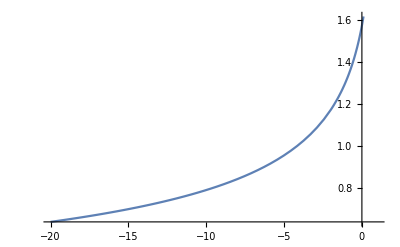

```mathematica
Plot[EllipticK[x],{x,-1,1}]
```

```mathematica
ind = ∫1/((a-x)(b-x)(c- x))^(1/2)ⅆx
```

(2 (a-x)^(3/2) √((b-x)/(a-x)) √((c-x)/(a-x)) EllipticF[ArcSin[(√(a-b))/(√(a-x))],(a-c)/(a-b)])/(√(a-b) √((a-x) (-b+x) (-c+x)))

```mathematica
ind2=Simplify[ind,a<x<c<b]
```

2 √(1/(a-b)) EllipticF[ArcSin[√((-a+b)/(b-x))],(-b+c)/(a-b)]

```mathematica
fin =Limit[ind2,x->c, Direction->"FromBelow"]
```

2 √(1/(a-b)) EllipticF[(√((-a+b)/(b-c)) √(b-c) ArcSin[(√(-a+b))/(√(b-c))])/(√(-a+b)),(-b+c)/(a-b)]

```mathematica
in = Limit[ind2,x->a, Direction->"FromAbove"]
```

2 √(1/(a-b)) EllipticK[(-b+c)/(a-b)]

```mathematica
fmi = Simplify[fin -in,a<x<c<b]
```

2 √(1/(a-b)) (EllipticF[ArcSin[√((-a+b)/(b-c))],(-b+c)/(a-b)]-EllipticK[(-b+c)/(a-b)])

```mathematica
Simplify[(-b+c)/(a-b)<1,a<x<c<b]
```

True

```mathematica
FunctionExpand[EllipticF[ArcSin[1/(√m)],m],0<m<1]
```

EllipticK[1/m]/(√m)

```mathematica
a=0.1
c=0.2
b=0.4
fmi
```

0.1

0.2

0.4

-6.33137+0. ⅈ

```mathematica
EllipticK[(-b+c)/(a-b)]
```

2.02896

```mathematica
Simplify[D[2/(√(c-a)) EllipticF[ArcSin[(√(a-x))/(√(a-b))],(b-a)/(c-a)] ,x] ,a<x<b<c]//Simplify

This one!!!! From here....
```

```mathematica
pr= 2/(√(c-a)) EllipticF[ArcSin[√((x-a)/(b-a))],(b-a)/(c-a)]
```

(2 EllipticF[ArcSin[√((-a+x)/(-a+b))],(-a+b)/(-a+c)])/(√(-a+c))

```mathematica
Simplify[D[pr,x],a<x<b<c]//Simplify
```

1/(√((b-x) (c-x) (-a+x)))

```mathematica
pr/.x->b
```

(2 EllipticK[(-a+b)/(-a+c)])/(√(-a+c))

```mathematica
pr/.x->a
```

0

```mathematica
To here....
```

```mathematica
dgg= 1/(√((x-a) (b-x) (c-x)))
 gg=   2/(√(c-a)) EllipticF[ArcSin[√((x-a)/(b-a))],(b-a)/(c-a)] 
ff = x
```

1/(√((b-x) (c-x) (-a+x)))

(2 EllipticF[ArcSin[√((-a+x)/(-a+b))],(-a+b)/(-a+c)])/(√(-a+c))

x

```mathematica
Simplify[D[gg,x],a<x<b<c]-dgg
```

0

```mathematica
dff = D[x,x]
```

1

```mathematica
num =Simplify[ff gg - Integrate[  gg ,x] dff,a<x<b<c]
```

(2 ((a-c) EllipticE[ArcSin[√((a-x)/(a-b))],(a-b)/(a-c)]+c EllipticF[ArcSin[√((a-x)/(a-b))],(a-b)/(a-c)]))/(√(-a+c))

```mathematica
(2 (c EllipticF[ArcSin[√((a-x)/(a-b))],(a-b)/(a-c)]- (c-a) EllipticE[ArcSin[√((a-x)/(a-b))],(a-b)/(a-c)]))/(√(c-a))//TeXForm
```

\frac{2 \left(c F\left(\sin
   ^{-1}\left(\sqrt{\frac{a-x}{a-b}}\right)|\frac{a-b}{a-c}\right)-(
   c-a) E\left(\sin
   ^{-1}\left(\sqrt{\frac{a-x}{a-b}}\right)|\frac{a-b}{a-c}\right)\r
   ight)}{\sqrt{c-a}}

```mathematica
num//TeXForm
```

\frac{2 \left(c F\left(\sin
   ^{-1}\left(\sqrt{\frac{a-x}{a-b}}\right)|\frac{a-b}{a-c}\right)+(
   a-c) E\left(\sin
   ^{-1}\left(\sqrt{\frac{a-x}{a-b}}\right)|\frac{a-b}{a-c}\right)\r
   ight)}{\sqrt{c-a}}

```mathematica
Simplify[D[num,x],a<x<b<c]
```

x/(√((-a+x) (-b+x) (-c+x)))

```mathematica
num/. x->a
```

0

```mathematica
Simplify[num/. x->b,a<x<b<c]
```

(2 ((a-c) EllipticE[(a-b)/(a-c)]+c EllipticK[(a-b)/(a-c)]))/(√(-a+c))

```mathematica
(2 (c EllipticK[(a-b)/(a-c)]-(c-a) EllipticE[(a-b)/(a-c)]))/(√(c-a))//TeXForm
```

\frac{2 \left(c K\left(\frac{a-b}{a-c}\right)-(c-a)
   E\left(\frac{a-b}{a-c}\right)\right)}{\sqrt{c-a}}

```mathematica
((2 ((a-c) EllipticE[(a-b)/(a-c)]+c EllipticK[(a-b)/(a-c)]))/(√(-a+c)))/((2 EllipticK[(-a+b)/(-a+c)])/(√(-a+c)))
```

((a-c) EllipticE[(a-b)/(a-c)]+c EllipticK[(a-b)/(a-c)])/EllipticK[(-a+b)/(-a+c)]

```mathematica
((2 (c EllipticK[(a-b)/(a-c)]-(c-a) EllipticE[(a-b)/(a-c)]))/(√(c-a)))/((2 EllipticK[(-a+b)/(-a+c)])/(√(-a+c)))//Simplify
```

c+((a-c) EllipticE[(a-b)/(a-c)])/EllipticK[(a-b)/(a-c)]

```mathematica
Solve [(b-a)/(c-a)==m,c]
```

{{c→(-a+b+a m)/m}}

```mathematica
c+(a-c) EoverM/.c->(-a+b+a m)/m//Simplify
```

(b-b EoverM+a (-1+EoverM+m))/m

```mathematica
my = a+ (b-a)/m(1-EoverM)
```

a+((-a+b) (1-EoverM))/m

```mathematica
my -((b-b EoverM+a (-1+EoverM+m))/m)//Simplify
```

0

```mathematica
my =(a+b)/2+ (b-a)/2(2/m(1-EoverM) - 1)
```

(a+b)/2+1/2 (-a+b) (-1+(2 (1-EoverM))/m)

```mathematica
my - (b-b EoverM+a (-1+EoverM+m))/m//Simplify
```

0

```mathematica
Series[(1/m)(1-EllipticE[m]/EllipticK[m]),{m,1,0}]
```

(Floor[-Arg[-1+m]/(2 π)] O[m-1]^1+Floor[-Arg[-1+m]/(2 π)] (-ⅈ π+O[m-1]^1)+(-1/2 ⅈ (-2 ⅈ+π+4 ⅈ Log[2]-ⅈ Log[-1+m])+O[m-1]^1))/(Floor[-Arg[-1+m]/(2 π)] (-ⅈ π+1/4 ⅈ π (m-1)+O[m-1]^2)+(-1/2 ⅈ (π+4 ⅈ Log[2]-ⅈ Log[-1+m])+1/8 ⅈ (-2 ⅈ+π+4 ⅈ Log[2]-ⅈ Log[-1+m]) (m-1)+O[m-1]^2))

```mathematica
Limit[2/m(1-EllipticE[m]/EllipticK[m])-1,m->1]
```

1

```mathematica
Limit[(1/m)(1-EllipticE[m]/EllipticK[m]),m->0]
```

1/2

```mathematica
(1/m)(1-EllipticE[m]/EllipticK[m])/.m->1
```

1

```mathematica
Clear@@DeleteCases[Names@"`*","ToPython"|"precessionform"]
```

```mathematica
DSolve[{k'[u]==(1/u)(k[u]- chieffM2 /2),k[u0]==k0},k[u],u]//Simplify
k[u]/.%[[1]]/.u-> (1+q)^2/ (2 q) /Sqrt[r]/.u0-> (1+q)^2/ (2 q) /Sqrt[r0]//Simplify
```

{{k[u]→(2 k0 u+chieffM2 (-u+u0))/(2 u0)}}

(chieffM2 (√r-√r0)+2 k0 √r0)/(2 √r)

```mathematica
Collect[%,r]//Simplify
```

1/2 (chieffM2-((chieffM2-2 k0) √r0)/(√r))

```mathematica
1/2 (chieffM2-((chieffM2-2 k0) √r0)/(√r))
```

((k0 (1+q)^2)/(q √r)+chieffM2 (-(1+q)^2/(2 q √r)+u0))/(2 u0)

```mathematica
,u]
```

chieffM2/2+((-chieffM2+2 k0) u)/(2 u0)

```mathematica
u = (1+q)^2/ (2 q) /Sqrt[r]
```

(1+q)^2/(2 q √r)

```mathematica
D[u,r]
```

-(1+q)^2/(4 q r^(3/2))

```mathematica
(1+q)^2/ (2 q) /Sqrt[r]
```

(1+q)^2/(2 q √r)

```mathematica
dhee
```

dhee